## A. GetVariance[ns, nph, Δprior] function

```mathematica
GetVariance[NumShots_,NumPhotons_,Δprior_]:=Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,φ,r,θ,Pmϕ,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*Uncertainty prior to this shot*)
Δ = Δprior;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
(*Δ here is centered around ϕ*)
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)
(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*The original integral (Check:1.3(Changes).nb): listOfϕ1 = Subscript[ϕ̃, m] = ParallelTable[ Integrate[ϕ listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Integrate[listOfPmϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];*)
(*The denominator of this integral is Pm/Pϕ*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
Pm = Pϕ Table[Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 =
ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
(*finalVariance is the weighted average variance of all the probable outcomes*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*for feedfoward, we need to output the variance for each of the probable outcomes - no sum*)
(*different normalization term eq17*)
listOfPartialVarianceFeedforward =normalizationTerm*Table[Re[dummyFinalVariance1[[j]]], {j,1,(nph+1)^ns}];
(*conditional probabilities*)
(*Print[listOfPmϕ];*)
(*phase estimator after measurement assuming outcome m*)
listOfϕ1Feedforward = Table[r[[1,n]]^2*listOfϕ1[[n]],{n,1,nph+1}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
(*Return[finalVariance]*)
Return[listOfPartialVarianceFeedforward]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## B. Optimal input states functions

```mathematica
PlugN00NSBS[]:=
Block[{},
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
(*finalVarianceN00N=finalVariance/.substlistN00N;*)
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
(*Print[substlistN00N];*)
(*returns the variance and state to be plugged in*)
Return[{substlistN00N}];]
```

```mathematica
PlugGSBS[]:=
Block[{},Clear[ρ3];
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1θ,substlistG1r}];
(*finalVarianceG1=finalVariance/.substlistG1;*)
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
(*Print[substlistG1];*)
(*This returns the state to be plugged in*)
Return[{substlistG1}];];
```

## (For check only) Adaptive global method - GetVffExact[NumShots_,NPhotons_,Δprior_]

```mathematica
GetVffExact[NumShots_,NPhotons_,Δprior_]:= 
Block[{IndVariance,rSubsList,θSubsList,listOfPmϕ,VffExact},
ns = NumShots;
nph = NPhotons;
Δ = Δprior;

IndVariance=GetVariance[ns,nph,Δ];
(*change variables of prob in such a way so as to differentiate between the two 1st shot outcomes*)
(*rVarChanged and θVarChanged need to be global since they are used in 3.ExtractOptState function*)
rVarChanged=Table[Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
θVarChanged=Table[Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[m1]],{k,0,nph}],{m1,1,nph+1}],{l,2,ns}];
rSubsList = Transpose[Table[Table[r[[2,b]]-> rVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
θSubsList = Transpose[Table[Table[θ[[2,b]]-> θVarChanged[[1,a,b]],{a,1,nph+1}],{b,1,nph+1}]];
(*Substitution list*)
SubsList = Table[Flatten[{rSubsList[[m1]],θSubsList[[m1]]}],{m1,1,nph+1}];
(*Substituting variables in the individual variance expressions*)
IndVarianceSub = Table[IndVariance[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
(*listOfPm2m1ϕ = P(m1|ϕ)P(m2|ϕ,m1)*)
listOfPmϕ;
(*listOfPm2m1ϕ = Table[listOfPmϕ[[n]]/.SubsList[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];*)
(*Normalize probability*)
(*each product normalizes 1 probability term in the product (of listOfPm2m1ϕ); e.g (1 /(r0s1^2+r1s1^2)) normalizes Pm#ϕs1*)
ListOfnormalizationTerms = Table[1/(∑_(s=1)^(nph+1) (r[[1,s]])^2)1/(∑_(s=1)^(nph+1) (rVarChanged[[1,i,s]])^2),{i,1,nph+1}];
(*listOfPm2m1ϕ= Table[listOfPm2m1ϕ[[n]]*ListOfnormalizationTerms[[Ceiling[n/(nph+1)]]],{n,1,(nph+1)^ns}];
Pm2m1 = Table[Integrate[Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}],{n,1,(nph+1)^ns}];
ϕm2m1 = Table[Integrate[ϕ Pϕ listOfPm2m1ϕ[[n]],{ϕ,-Δ/2,Δ/2}]/Pm2m1[[n]],{n,1,(nph+1)^ns}];*)
Wm = Table[ListOfnormalizationTerms[[Ceiling[m2/(nph+1)]]]*IndVarianceSub[[m2]],{m2,1,(nph+1)^ns}];
VffExactInd=Partition[Wm,nph+1];
VffExactIndSum = Table[Total[VffExactInd[[n]]],{n,1,nph+1}];
VffExact = Sum[Wm[[m1]],{m1,1,Length[Wm]}];
Return[VffExactIndSum]
]
```

#### Checks

```mathematica
(*Probability*)
```

```mathematica
Checksub=Flatten[{{θ0s1->2.851490288263774},{θ1s1->0.25304094804538657},{θ2s1->-1.4739933234649785},{θ0s2m1->-3.093399176686934},{θ1s2m1->1.553767334364549},{θ2s2m1->2.4567718694141494},{θ0s2m2->-3.0911976444251295},{θ1s2m2->1.670070365372295},{θ2s2m2->2.4969781506465303},{θ0s2m3->-2.0057741338419515},{θ1s2m3->1.9589500610781467},{θ2s2m3->-2.17469519303548},{r0s1->0.062327025905407174},{r1s1->0.7408594969868596},{r2s1->0.5277260482635109},{r0s2m1->0.2979036019318746},{r1s2m1->0.13897817556102043},{r2s2m1->0.2456424044272012},{r0s2m2->0.578500557504519},{r1s2m2->0.8314464160878037},{r2s2m2->0.10511807207960588},{r0s2m3->0.3259088817360256},{r1s2m3->0.2749830952433989},{r2s2m3->0.014299502030310274}}]
```

{θ0s1→2.85149,θ1s1→0.253041,θ2s1→-1.47399,θ0s2m1→-3.0934,θ1s2m1→1.55377,θ2s2m1→2.45677,θ0s2m2→-3.0912,θ1s2m2→1.67007,θ2s2m2→2.49698,θ0s2m3→-2.00577,θ1s2m3→1.95895,θ2s2m3→-2.1747,r0s1→0.062327,r1s1→0.740859,r2s1→0.527726,r0s2m1→0.297904,r1s2m1→0.138978,r2s2m1→0.245642,r0s2m2→0.578501,r1s2m2→0.831446,r2s2m2→0.105118,r0s2m3→0.325909,r1s2m3→0.274983,r2s2m3→0.0142995}

```mathematica
Sum[Pm2m1[[n]],{n,1,Length[Pm2m1]}]/.Checksub/.{Δ->π}
```

1.-2.11249×10^-18 ⅈ

```mathematica
(*Variance*)
```

## Simulation for MCA

### Comparing MC A with Analytic A, for N=4 (Scalable)

#### MC Adaptive

```mathematica
MCAVaryΔ = Table[VarRatioϕtrueGrid=Table[
ntrial=100;
listOfVarRatio=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =n π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.UnshiftedOptState/.ϕ->(ϕTrue)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Probability1stshot=prob2[[1,outcomeOccured]];
(*normalize variance*)
normalizedvariance=variance;
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{normalizedvariance/(initInterval^2/12),ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}
,{shot,1, nshots}],{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{initInterval, Mean[listOfVarRatio[[All,2,1]]],phitrue},{phitrue,-initInterval/3,initInterval/3,initInterval/10}];
(*mean VarRatio averaged over uniform grid of ϕtrue*)
Flatten[{initInterval, Mean[VarRatioϕtrueGrid[[All,2]]]}],{n,1,10}];
```

```mathematica
VarRatioϕtrueGrid
```

{{π/10,0.799546,-π/30},{π/10,0.764048,-(7 π)/300},{π/10,0.799546,-π/75},{π/10,0.799546,-π/300},{π/10,0.799546,π/150},{π/10,0.799546,π/60},{π/10,0.764048,(2 π)/75}}

```mathematica
(*{ϕtrue, probability of 1shot outcome, probability of 2nd shot outcome, partial variance for the particular 1st shot outcome, 1st shot outcome*)
```

```mathematica
MCAVaryΔ
```

{{π/10,0.77419},{π/5,0.443015},{(3 π)/10,0.236116},{(2 π)/5,0.349789},{π/2,0.353799},{(3 π)/5,0.27781},{(7 π)/10,0.292475},{(4 π)/5,0.110457},{(9 π)/10,0.1135},{π,0.0786249}}

{0.77419,0.443015,0.236116,0.349789,0.353799,0.27781,0.292475,0.110457,0.1135,0.0786249}

#### VarRatio MCSA, MCA with sbs optimal states plugged into global variance N=4, ns=2

```mathematica
(*Non-adaptive global*)
```

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
(*MonteCarlo Semi-Adaptive*)
```

```mathematica
MCSAPlugged={0.7832548199807943,0.44909545514972116,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.28673863672037136,0.23189593990295332,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*Semi-adaptive*)
```

```mathematica
AnalyticSA={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*MonteCarlo Adaptive 10 trials of 100 phitrue intervals (1000 total)*)
```

```mathematica
MCAPluggedScalable1=MCAVaryΔ[[All,2]]
```

{0.77419,0.443015,0.236116,0.349789,0.353799,0.27781,0.292475,0.110457,0.1135,0.0786249}

```mathematica
MCAPluggedScalable10=MCAVaryΔ[[All,2]]
```

{0.771655,0.400282,0.25483,0.381863,0.370364,0.335653,0.26308,0.117608,0.111415,0.110515}

```mathematica
MCAPluggedScalable100=MCAVaryΔ[[All,2]]
```

{0.773278,0.419779,0.257771,0.381889,0.37747,0.363843,0.280991,0.121726,0.106112,0.106656}

```mathematica
(*Adaptive*)
```

```mathematica
AnalyticA ={0.7848048836429581,0.4669568863147173,0.29662564242447337,0.29568912007540094,0.2519147001923571,0.19472241150788455,0.16801400651733248,0.12769682385452574,0.11170264823418144,0.1024495735826159}
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

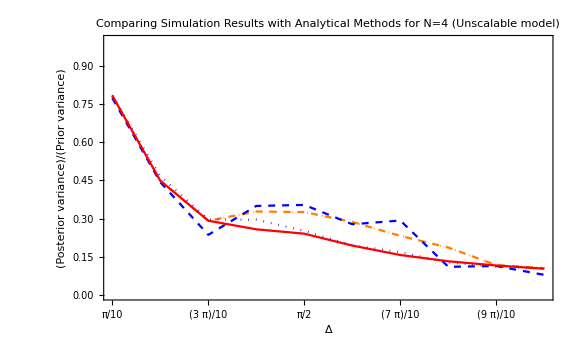

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged1,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

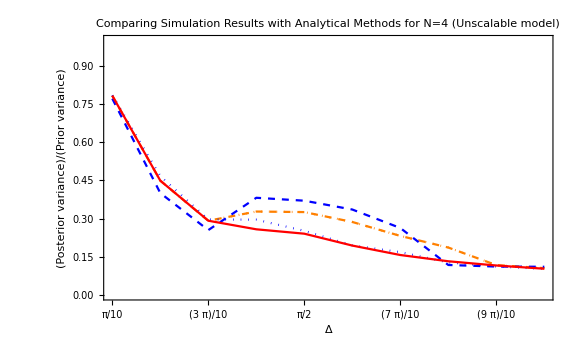

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPluggedScalable10,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 10 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

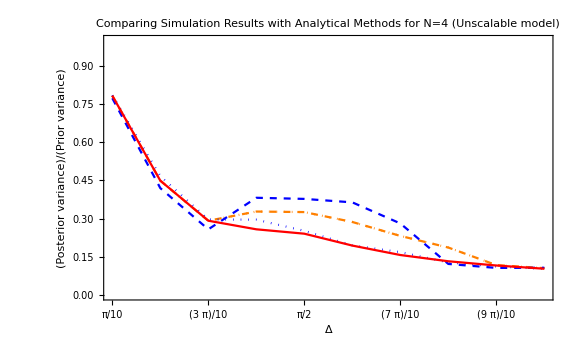

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPluggedScalable100,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 100 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

### Comparing MC A with Analytic A, for N=4 (unscalable - plug apt states into global variance)

#### MC Adaptive

```mathematica
MCAVaryΔ=Table[
ntrial=10;
MCATrial=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =n π/10;
GlobalVarianceA=GetVffExact[2,nph,initInterval];
VarRatio=Table[
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=2;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.UnshiftedOptState/.ϕ->(ϕTrue)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
{variance,phitrue,ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}
,{shot,1, nshots}];
(*save the 2 shot outcomes*)
TwoShotOutcomesFixed={phitilde[[1,6]],phitilde[[2,6]]};
(*1st shot outcome*)
OutcomeOccured1stShot=phitilde[[1,6]];
(*For the first shot*)
Shot1AptStateList=phitilde[[1,5,1]];
Shot2AptStatetempList=phitilde[[2,5,1]];
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]<>"m"<>ToString[OutcomeOccured1stShot]],{k,0,nph}],{l,1,2}];
(*Change variable names for second shot*)
Shot2AptStateList=Flatten[Table[{θ[[2,n]]-> Shot2AptStatetempList[[n,2]],r[[2,n]]-> Shot2AptStatetempList[[n+nph+1,2]]},{n,1,nph+1}]];
(*Substitution list*)
AptStates = Join[Shot1AptStateList,Shot2AptStateList];
(*Calculate the average phase estimator after 100 trials of 2 shots*)
ϕm1m2=phitilde[[2,3]];
(*outcome, probability1, probability2*)
probability1= {phitilde[[1,8]],phitilde[[2,8]]};
(*1st shot probability*)
Probability1stshot=phitilde[[1,8]][[1,OutcomeOccured1stShot]];
(*Normalized variance*)
variance2=GlobalVarianceA[[OutcomeOccured1stShot]]/.AptStates;
normalizedvariance=variance2/Probability1stshot;
(*VarianceRatio*)
BMSERatio = normalizedvariance/(initInterval^2/12);
(*ϕTrue, probability of 1st shot outcomes, probability of 2nd shot outcomes, variance*)
{phitrue,probability1,variance2,OutcomeOccured1stShot,BMSERatio},{phitrue,-initInterval/2,initInterval/2,initInterval/100}];
PartialVariances=VarRatio[[All,3]];
normalizedPartialVariance=Mean[VarRatio[[All,5]]];
normalizedPartialVariance,{trial,1,ntrial}];
Mean[MCATrial],{n,1,10}];
```

```mathematica
GlobalVarianceA[[OutcomeOccured1stShot]]
```

(10 Re[5+2 (-(3 ⅇ^(ⅈ θ0s1+5) (12/5 (-1-√5) π-√1 1) r0s1 r0s2m4 r4s1 r4s2m4)/32768+1/10368+5+1/48 (1) (6/5 π Cos[(3 π)/20]+(-8+(9 1)/100) Sin[1/20]))])/(3 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)+(10 Re[1])/(3 π (r0s1^2+3+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)+(10 Re[1])/(3 π 1^2 (1)^2)+(10 Re[5+2 (1)])/(3 π (1)^2 (r0s2m4^2+3+r4s2m4^2)^2)+(10 Re[5+2 (-(ⅇ^1 4 r4s2m4)/65536+6+1/288 (1) (1))])/(3 π (r0s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2)^2 (r0s2m4^2+r1s2m4^2+r2s2m4^2+r3s2m4^2+r4s2m4^2)^2)
 |  |  |  |

```mathematica
(*{ϕtrue, probability of 1shot outcome, probability of 2nd shot outcome, partial variance for the particular 1st shot outcome, 1st shot outcome*)
```

```mathematica
MCAVaryΔ
```

{0.79585,0.465726,0.2893,0.276689,0.248536,0.183843,0.169411,0.10862,0.0881129,0.0772369}

#### Checks

```mathematica
(*1st and 2nd shot outcomes*)
```

```mathematica
(*Outcomes occured*)
```

```mathematica
TwoShotOutcomesFixed
```

{2,3}

```mathematica
(*1st shot probability*)
```

```mathematica
Mean[VarRatio[[All,2,1]]]
```

{{0.0586102,0.256552,0.369676,0.256552,0.0586102}}

```mathematica
(*2nd shot probability*)
```

```mathematica
Mean[VarRatio[[All,2,2]]]
```

{{0.0625,0.25,0.375,0.25,0.0625}}

```mathematica
(**)
```

```mathematica
Mean[VarRatio[[All,2,1]]]
```

{{0.0586102,0.256552,0.369676,0.256552,0.0586102}}

```mathematica
phitilde[[1,8]]
```

{{0.00128392,0.0000173272,0.158047,0.577303,0.263348}}

```mathematica
OutcomeOccured1stShot
```

2

```mathematica
AptStates
```

{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641,θ0s2m2→-0.197425,r0s2m2→1/(√2),θ1s2m2→-1.66816,r1s2m2→0,θ2s2m2→2.21337,r2s2m2→0,θ3s2m2→-1.97867,r3s2m2→0,θ4s2m2→-2.94576,r4s2m2→1/(√2)}

```mathematica
NumOfOccurance
```

{1,0,0,0,0}

```mathematica
MCAVaryΔ
```

{{Probability1stShot,0.00956584}}

```mathematica
indvar={0.0010991090804640198,0.008688934533352777,0.019494074919258513,0.008688934533352767,0.0010991090804640148}
```

{0.00109911,0.00868893,0.0194941,0.00868893,0.00109911}

```mathematica
NumOfOccurance
```

{3,5,2,0,0}

```mathematica
Inner[Times,indvar,NumOfOccurance,Plus]
```

0.18664

```mathematica
(*variance - after shot 1 and 2*)
```

```mathematica
phitilde[[All,1]]
```

{0.0561993,0.0691783}

```mathematica
(*Mean of variance. The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}.*)
```

```mathematica
Mean[MCAVaryΔ[[1,All,3]]]
```

0.0342622

```mathematica
0.013600361981491753/0.25655176127787704
```

0.0530122

```mathematica
(*uncertainties - after shot 1 and shot 2*)
```

```mathematica
N[initInterval]
```

1.25664

```mathematica
phitilde[[All,7]]
```

{0.571295,0.703762}

```mathematica
(*optimal input states - shots 1 and 2*)
```

```mathematica
phitilde[[All,5]]
```

{{{θ0s1→0,θ1s1→π/2,θ2s1→π,θ3s1→(3 π)/2,θ4s1→2 π,r0s1→0.401641,r1s1→0.467013,r2s1→0.491087,r3s1→0.467013,r4s1→0.401641}},{{θ0s1→-0.886533,θ1s1→0.972221,θ2s1→-0.36039,θ3s1→3.23514,θ4s1→-0.715884,r0s1→1/(√2),r1s1→0,r2s1→0,r3s1→0,r4s1→1/(√2)}}}

```mathematica
VarRatio
```

{{4,{{0.00128392,0.0000173272,0.158047,0.577303,0.263348}},{{0.0526534,0.289386,0.315921,0.289386,0.0526534}}}}

```mathematica
MCAVaryΔ[[All,2]];
```

```mathematica
MCAVaryΔ[[All,3]];
```

```mathematica
(*probability of 1st shot outcomes*)
```

```mathematica
Table[Mean[MCAVaryΔ[[All,2,n]]],{n,1,5}]
```

{0.0512417,0.253726,0.390065,0.253726,0.0512417}

```mathematica
(*probability of 2nd shot outcomes*)
```

```mathematica
Table[Mean[MCAVaryΔ[[All,3,n]]],{n,1,5}]
```

{0.0625,0.25,0.375,0.25,0.0625}

```mathematica
MCAVaryΔ
```

{{-π/5,0.262366}}

```mathematica
(*probabilities of 1st shot outcomes*)
```

```mathematica
phitilde[[All,8]]
```

{{{0.263348,0.577303,0.158047,0.0000173272,0.00128392}},{{0.123281,0.00687475,0.739688,0.00687475,0.123281}}}

```mathematica
Mean[{0.26334795992165755,0.5773034743958148,0.15804731556906382,0.000017327191833854955,0.00128392292162977}]
```

0.2

```mathematica
phitilde[[All,1]]
```

{0.0561993,0.0691783}

```mathematica
(*Mean Variance Ratio for N=4,Δ=3π/10 *)
```

```mathematica
Mean[MCAVaryΔ[[All,2]]]
```

0.487872

```mathematica
(*Here's what I had before*)
```

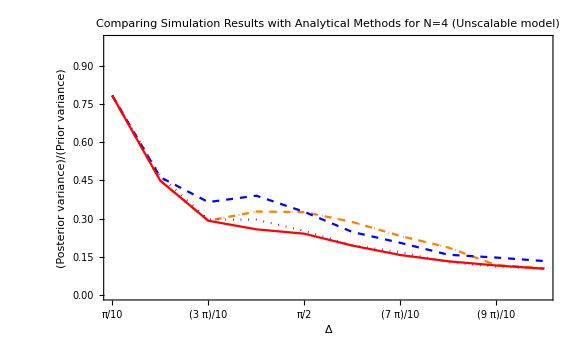

```mathematica
(*Needs to be 0.29662564242447337*)
```

```mathematica
(*(*Normalization term depending on the measurement outcome?*)
(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
NormalizationTerm=∏_(i=1)^2 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
NormalizedBMSE = NormalizationTerm*BMSE/.AptStates;*)
```

#### Compare plots for N=4

```mathematica
MCA=MCAVaryΔ
```

{0.791559,0.446835,0.312248,0.287299,0.206233,0.134921,0.0910083,0.0672826,0.0779839,0.0485061}

```mathematica
MCA={0.7750201854703866,0.4942465681238499,0.3374615958772505,0.3452534692001444,0.2860898224128942,0.25007547813932435,0.17765369341379555,0.13153606847444343,0.11785530468575152,0.11670880858745618}
```

{0.77502,0.494247,0.337462,0.345253,0.28609,0.250075,0.177654,0.131536,0.117855,0.116709}

```mathematica
MCSA = {0.7837398433677253,0.4536090556738001,0.2739163064796318,0.2350774296474307,0.17770750155811743,0.14374881829066774,0.12245895320127148,0.10885047118339157,0.1044535037354056,0.08868957807323821}
```

{0.78374,0.453609,0.273916,0.235077,0.177708,0.143749,0.122459,0.10885,0.104454,0.0886896}

```mathematica
AnalyticA ={0.0064547614446658005,0.015362265800969058,0.02195683309461405,0.03891112854467223,0.051797884035783205,0.057654995088268504,0.06771113094186494,0.06721691385172052,0.07441611403221542,0.0842613968600595}
```

{0.00645476,0.0153623,0.0219568,0.0389111,0.0517979,0.057655,0.0677111,0.0672169,0.0744161,0.0842614}

```mathematica
AnalyticA=Table[AnalyticA[[n]]/((n π/10)^2/12),{n,1,10}]
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
AnalyticSA ={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
OptimalSA = {0.7832548199808358,0.4490954551497609,0.29166028593618665,0.26058612809564585,0.2406540258448837,0.19393250958529862,0.1567902732388312,0.13218789349385024,0.11558869633632414,0.10285374254650627}
```

{0.783255,0.449095,0.29166,0.260586,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

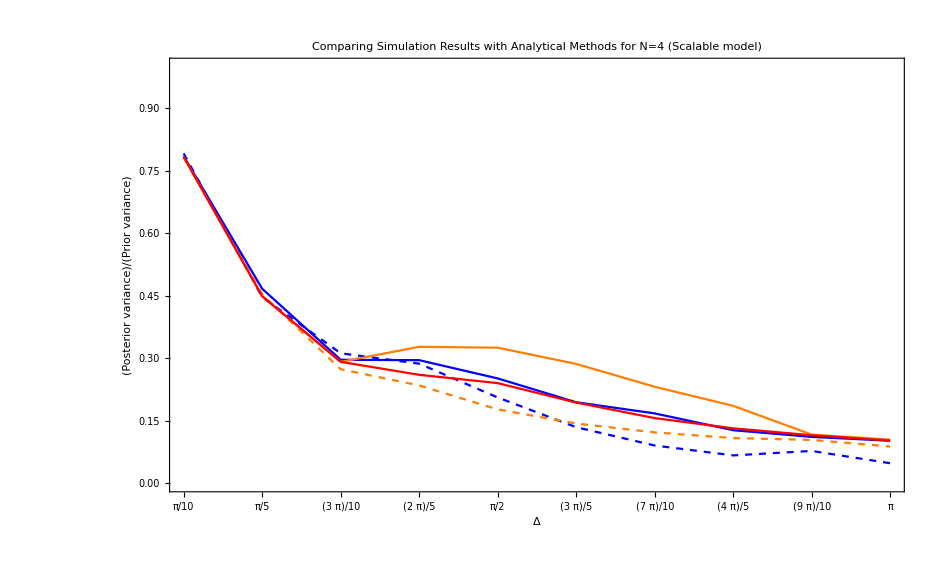

```mathematica
Show[ListLinePlot[MCA,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA"},{Right,Top}]],ListLinePlot[MCSA,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue},PlotLegends->Placed[{"Analytic Adaptive"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange},PlotLegends->Placed[{"Analytic Semi-Adaptive"},{Right,Top}]],ListLinePlot[OptimalSA,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Scalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize-> Large]
```

#### VarRatio MCSA, MCA with sbs optimal states plugged into global variance N=4, ns=2

```mathematica
(*Non-adaptive global*)
```

```mathematica
VRO4={0.7832548199809993,0.4490954551498136,0.29166028593590415,0.25787058571642585,0.24065402584283038,0.19393250958543157,0.15679027323873104,0.13218789349294494,0.11558869633651987,0.1028537425463464}
```

{0.783255,0.449095,0.29166,0.257871,0.240654,0.193933,0.15679,0.132188,0.115589,0.102854}

```mathematica
(*MonteCarlo Semi-Adaptive*)
```

```mathematica
MCSAPlugged={0.7832548199807943,0.44909545514972116,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.28673863672037136,0.23189593990295332,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*Semi-adaptive*)
```

```mathematica
AnalyticSA={0.7832548199807943,0.4490954551497212,0.2916602859354953,0.3277416967803197,0.32562310100328096,0.2867386367203714,0.23189593990295326,0.18620363615424057,0.11710319710401186,0.10512412877158415}
```

{0.783255,0.449095,0.29166,0.327742,0.325623,0.286739,0.231896,0.186204,0.117103,0.105124}

```mathematica
(*MonteCarlo Adaptive 10 trials of 100 phitrue intervals (1000 total)*)
```

```mathematica
MCAPlugged10=MCAVaryΔ
```

{0.792134,0.479021,0.339269,0.263662,0.264563,0.182399,0.23943,0.0989743,0.0700832,0.0746591}

```mathematica
MCAPlugged100=MCAVaryΔ
```

{0.79585,0.465726,0.2893,0.276689,0.248536,0.183843,0.169411,0.10862,0.0881129,0.0772369}

```mathematica
MCAPlugged3=MCAVaryΔ
```

{0.798505,0.405386,0.225353,0.281024,0.263535,0.16197,0.157623,0.0834823,0.0734167,0.0614722}

```mathematica
(*Adaptive*)
```

```mathematica
AnalyticA ={0.7848048836429581,0.4669568863147173,0.29662564242447337,0.29568912007540094,0.2519147001923571,0.19472241150788455,0.16801400651733248,0.12769682385452574,0.11170264823418144,0.1024495735826159}
```

{0.784805,0.466957,0.296626,0.295689,0.251915,0.194722,0.168014,0.127697,0.111703,0.10245}

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

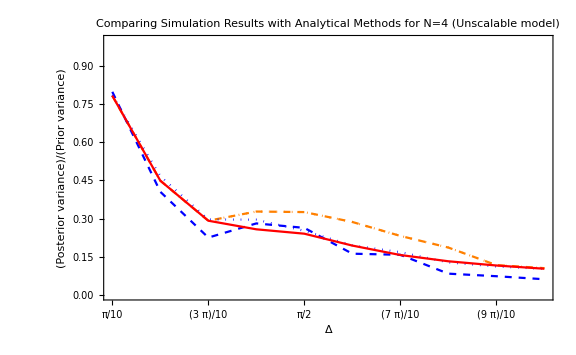

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged3,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

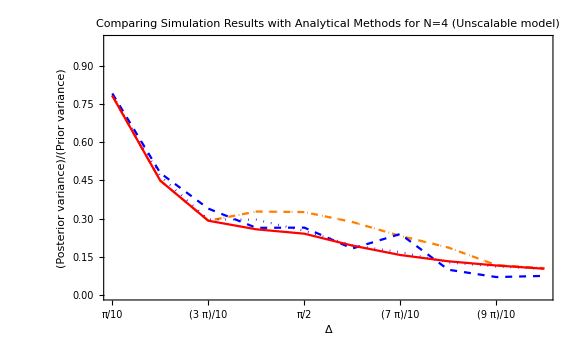

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged10,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 10 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

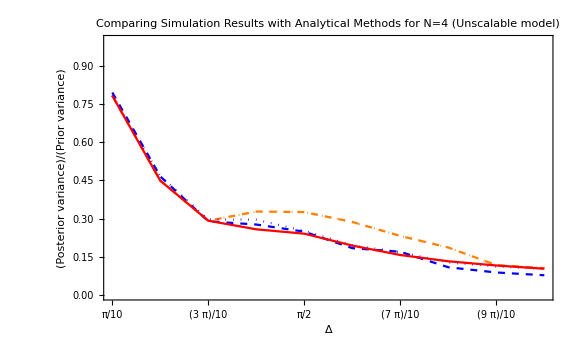

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged100,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 100 trials of 100 phitrue intervals"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

```mathematica
Show[ListLinePlot[MCSAPlugged,PlotStyle->{Orange,Dashed},PlotLegends->Placed[{"MCSA"},{Right,Top}]],ListLinePlot[AnalyticSA,PlotStyle->{Orange,Dotted},PlotLegends->Placed[{"Analytical semi adaptive"},{Right,Top}]],ListLinePlot[MCAPlugged3,PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"MCA 3 trials"},{Right,Top}]],ListLinePlot[AnalyticA,PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"Analytical adaptive"},{Right,Top}]],ListLinePlot[VRO4,PlotStyle->{Red},PlotLegends->Placed[{"Non-adaptive global"},{Right,Top}]],FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing Simulation Results with Analytical Methods for N=4 (Unscalable model)", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}},ImageSize->Large]
```

-Graphics-

## D. Error Analysis for 100 trials of 30 shots of N=3, Δinit=π

#### Error Analysis for 100 trials of 30 shots

```mathematica
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=4;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =π;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=30;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.UnshiftedOptState/.ϕ->(ϕTrue)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Probability1stshot=prob2[[1,outcomeOccured]];
(*normalize variance*)
normalizedvariance=variance;
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
(*{normalizedvariance/(initInterval^2/12),ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}*)
Δnext
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,listOfPhaseEstimators},{phitrue,-1.5,1.5,0.3}];
```

```mathematica
{ntrial,nshots}
```

{100,10}

```mathematica
(*{ϕtrue, {{Δ,ϕ̃(after 100 shots for trial 1)} , {Δ,OverTilde[ϕ(after 100 shots for trial 2)]} ,...}}*)
```

```mathematica
MatrixForm[GridOfϕTrue]
```

(-1.5 | {{2.03191,-1.59604},{0.31807,-1.94847},{0.188976,-1.42514},{0.641071,-1.18698},{0.356834,-1.76285},{0.594956,-2.00673},{1.92758,-2.1771},{0.722692,-1.13971},{0.448006,-2.74824},{0.797216,-1.57083},{1.32107,-1.55136},{2.03191,-1.59604},{0.716176,-1.14402},{1.04598,-2.00218},{3.34023,-0.974077},{1.61484,-2.1027},{0.210002,-1.22875},{0.920837,-1.18537},{0.57595,-1.97077},{1.60194,-1.46277},{0.185891,-1.97647},{0.623283,-2.04185},{1.79492,-1.48619},{0.312524,-1.10654},{0.89403,-1.12833},{0.154184,-1.20483},{0.114851,-1.89378},{2.06011,-1.32234},{0.203177,-1.51923},{0.877991,-1.91347},{0.824975,-1.13507},{1.67742,-1.33287},{1.62589,-1.16686},{2.01662,-1.65747},{2.03954,-1.57244},{0.0707738,-1.17011},{1.62166,-2.01896},{1.62066,-1.10599},{0.684094,-1.23246},{0.541767,-1.1825},{0.815987,-1.95379},{0.411371,-1.78677},{0.187866,-1.70019},{0.273313,-1.36872},{1.97338,-1.6328},{2.02905,-1.59109},{0.717407,-1.6781},{0.756784,-1.93903},{0.48695,-2.3709},{0.803354,-1.18136},{0.242021,-0.390872},{0.385495,-1.93271},{0.480345,-1.16191},{0.600659,-1.14481},{1.33616,-1.95529},{2.599,-1.68423},{2.02933,-1.58822},{0.616637,-1.18697},{2.03821,-1.58149},{2.73711,-0.444649},{1.54,-1.18139},{2.0246,-1.58837},{1.38501,-1.16835},{1.20942,-1.95881},{0.811358,-1.28029},{1.65193,-0.9269},{0.100726,-1.17352},{0.991632,-1.1662},{0.0501999,-1.18071},{1.6178,-2.06813},{0.0824441,-1.2156},{1.61427,-2.11744},{1.13171,-1.95642},{2.02372,-1.54869},{0.0895948,-1.23384},{0.475724,-1.76058},{1.75385,-1.5749},{0.0543425,-1.96842},{0.0664182,-1.93384},{0.461962,-1.67731},{2.03771,-1.56502},{1.56393,-1.18487},{1.61985,-1.09619},{2.03588,-1.57082},{0.529479,-1.18204},{0.741542,-1.22379},{2.08678,-1.23042},{0.873212,-1.183},{1.58588,-1.95591},{1.62031,-0.965236},{2.03191,-1.59604},{0.228261,-1.83568},{0.960966,-1.57077},{0.7968,-1.9546},{0.359124,-1.94468},{0.334601,-1.79898},{1.61725,-1.06798},{0.528375,-2.04572},{0.688012,-1.93202},{0.814392,-1.28371}}
-1.2 | {{0.501412,-1.36521},{2.03026,-1.59371},{0.532236,-1.15594},{1.33998,-1.49162},{0.474071,-1.15952},{0.657341,-1.19101},{0.375275,-1.28263},{1.70618,-1.5713},{1.61389,-1.00718},{1.6193,-1.09675},{0.781374,-1.57126},{0.845031,-1.19408},{1.59728,-1.15177},{0.857168,-1.50854},{2.07023,-1.3711},{0.895998,-1.49958},{1.62501,-1.13677},{0.918146,-1.25445},{1.27539,-1.15813},{0.419151,-1.16129},{1.05815,-1.57079},{1.59608,-1.29054},{0.326219,-1.26219},{1.70945,-1.57386},{1.98428,-1.58139},{1.41833,-1.5367},{1.60348,-1.45341},{2.08185,-1.25486},{1.62297,-1.15993},{1.12106,-1.48355},{0.285293,-1.38727},{0.771903,-1.41782},{1.30351,-1.476},{1.26651,-1.16532},{1.92514,-1.84198},{1.74752,-1.57083},{1.67649,-0.916871},{1.59155,-1.31912},{1.52456,-1.15601},{1.7688,-1.58393},{1.60458,-1.44368},{0.584097,-1.39342},{1.53712,-1.51188},{1.44638,-1.45467},{1.78013,-1.80045},{0.436592,-1.1573},{1.30599,-1.47575},{1.7017,-1.56315},{0.843385,-1.25079},{1.33928,-1.24103},{1.40761,-1.20359},{1.62708,-1.1288},{0.790149,-1.53143},{1.62611,-1.13854},{1.76469,-1.57093},{1.65957,-1.57143},{1.58659,-1.18594},{1.62624,-1.14748},{0.679989,-1.20828},{1.64309,-1.31798},{1.81536,-1.49641},{0.191644,-1.16243},{1.25854,-1.47727},{1.1782,-1.16649},{1.56678,-1.57116},{0.984034,-1.56472},{1.66035,-0.922601},{1.60194,-1.46277},{0.518278,-1.15669},{2.00211,-1.5707},{0.831308,-1.1298},{1.616,-0.982512},{0.890789,-1.22947},{1.74887,-1.57112},{1.59529,-1.29096},{1.62368,-1.1817},{1.1782,-1.16649},{1.61418,-0.999465},{0.259689,-1.42381},{1.30753,-1.47555},{0.672686,-1.13869},{1.69,-1.57078},{1.5089,-1.17174},{1.79558,-0.918314},{1.59709,-1.19475},{0.296691,-1.16553},{0.671729,-1.30253},{1.61415,-1.02045},{1.41551,-1.5708},{1.03923,-1.57076},{1.31293,-1.15847},{1.60704,-1.17145},{1.62236,-1.19199},{1.6259,-1.13341},{1.06854,-1.15511},{1.62256,-1.14843},{1.7618,-1.5708},{0.805432,-1.16603},{1.57554,-1.25864},{1.00827,-1.20071}}
-0.9 | {{0.517289,-1.92614},{0.663036,-2.08645},{0.699678,-1.1152},{0.411777,-1.17326},{2.36489,-1.83855},{0.208474,-1.16921},{1.76266,-1.5708},{1.32848,-1.57076},{1.6408,-1.24081},{1.79692,-1.27404},{1.40633,-1.57079},{1.4031,-1.25757},{1.76906,-1.56745},{0.595027,-1.9193},{0.646953,-1.15758},{1.59102,-1.32535},{2.01465,-1.46974},{1.39868,-1.18903},{1.76792,-1.57932},{0.565018,-1.92512},{0.304891,-1.68806},{0.514052,-1.44565},{1.71174,-1.5708},{1.74172,-1.5708},{1.71204,-1.5708},{1.76349,-1.58193},{0.24698,-1.94819},{1.4739,-1.65969},{2.02223,-1.58888},{0.387858,-1.18501},{1.66983,-1.5708},{1.62613,-1.90071},{1.54886,-1.38381},{1.78459,-1.8292},{1.53481,-1.39955},{2.00404,-1.76163},{1.60991,-1.66872},{0.531206,-1.19233},{1.76045,-1.57008},{0.428229,-1.45764},{1.62282,-1.17821},{0.556039,-1.57908},{0.0430364,-1.17982},{0.79972,-1.98973},{1.09788,-1.18869},{1.68713,-1.40205},{0.419999,-1.9954},{1.05049,-1.99667},{1.76859,-1.57128},{1.66092,-1.32444},{1.65861,-1.59139},{1.34679,-1.19984},{0.762066,-1.16868},{0.708102,-1.13291},{1.11029,-1.15754},{0.46903,-1.93438},{1.63107,-1.5708},{1.76864,-1.57281},{0.187635,-1.16924},{0.929936,-1.14432},{0.0280752,-1.17937},{1.62718,-1.56925},{1.48491,-1.87631},{1.03113,-1.93449},{1.99563,-1.32273},{1.44106,-1.15265},{1.4357,-1.57566},{0.506586,-0.449971},{2.79703,-1.57807},{1.75295,-1.2699},{1.76088,-1.64043},{0.810939,-1.93479},{1.76874,-1.56056},{1.26388,-1.23257},{1.70175,-1.40888},{0.151865,-1.22508},{1.60724,-1.2385},{1.76594,-1.57245},{1.60556,-1.24389},{0.799691,-1.13825},{0.429953,-1.96753},{1.76322,-1.5708},{1.68725,-1.4075},{1.14525,-1.15038},{0.580028,-1.91164},{1.7331,-1.37782},{0.901995,-1.12814},{0.121958,-1.93339},{0.548979,-1.68619},{0.186749,-1.56008},{0.831271,-1.19278},{1.75519,-1.53533},{0.0586755,-0.413945},{0.700569,-1.22549},{0.230035,-1.17682},{0.362251,-1.35759},{1.55396,-1.38345},{0.321767,-1.97252},{0.283913,-1.1722},{1.57431,-1.24073}}
-0.6 | {{1.59778,-0.385298},{0.221492,-0.570322},{0.112412,-1.18469},{0.494679,-0.403004},{0.355138,-1.24921},{0.297512,-0.757203},{0.138224,-0.547533},{0.237317,-0.393876},{0.50214,-0.853037},{0.110328,-0.394642},{0.172345,-0.781059},{0.202707,-0.865043},{0.204429,-0.793509},{0.140349,-0.390831},{0.262131,-1.16754},{0.0341924,-0.393776},{1.02992,-0.681843},{0.349977,-1.05898},{1.58091,-0.393285},{0.192292,-1.00239},{0.0831691,-1.19484},{0.15598,-1.01772},{0.166436,-0.39527},{0.244688,-0.61257},{0.208284,-0.8161},{0.724134,-0.391193},{0.303917,-1.13613},{0.0865108,-1.21446},{0.298434,-0.395382},{0.619908,-0.395189},{0.162783,-0.999985},{1.53816,-0.390108},{0.378878,-0.394677},{0.26583,-0.463611},{0.25475,-1.1802},{0.47946,-0.382394},{0.726321,-0.386967},{0.6495,-0.401781},{0.352308,-0.87696},{0.534368,-0.391867},{0.198425,-0.418977},{0.570135,-0.391395},{0.375692,-1.17994},{0.780396,-1.16262},{1.43216,-1.96722},{0.249738,-0.389037},{0.590835,-0.383155},{0.288568,-0.814995},{0.778257,-0.84028},{0.0262413,-0.393107},{0.549439,-0.390592},{0.0429186,-1.9372},{0.288326,-1.12114},{1.26904,-0.38972},{0.289372,-0.380799},{0.0829454,-0.385328},{0.429576,-0.823955},{0.201037,-0.775154},{0.429727,-0.805715},{0.398741,-0.38405},{0.407935,-0.393846},{0.310659,-1.16332},{0.243316,-0.881031},{0.937909,-0.398393},{0.19087,-0.832282},{0.698747,-0.40059},{0.116501,-0.447497},{0.18354,-0.388328},{0.591556,-0.695838},{0.397634,-1.42173},{0.16736,-1.01583},{0.110188,-0.392047},{0.102615,-0.393747},{0.0836674,-1.89721},{0.433072,-1.24615},{0.318576,-0.720052},{0.491667,-0.632935},{0.0717109,-1.18296},{0.587264,-1.22266},{0.388192,-0.754941},{0.70279,-0.391813},{0.893641,-0.400099},{0.3001,-0.392775},{0.869782,-0.443811},{0.161696,-0.392304},{0.229821,-1.09929},{0.647124,-0.751891},{0.316712,-0.39137},{0.97632,-0.396945},{0.297938,-0.395128},{0.549526,-1.18108},{0.38093,-1.04904},{0.223478,-0.494076},{0.232975,-1.19956},{0.386716,-1.15509},{0.233688,-0.404856},{0.177283,-0.832877},{0.123198,-0.544395},{0.957139,-0.378506},{0.572046,-1.03425}}
-0.3 | {{2.02399,0.168337},{1.11865,-0.392654},{0.2068,-0.37582},{0.435306,-1.07033},{1.67268,1.52265},{1.05853,-0.43746},{2.3053,2.08662},{1.17205,-0.408014},{0.176657,-0.526496},{0.993847,-0.671476},{1.26904,-0.38972},{0.0530953,-0.394788},{0.253877,-0.406823},{1.58582,-0.386766},{0.395102,-0.39428},{1.17443,-0.393972},{0.231709,-0.396396},{0.692369,-0.408361},{0.89765,-0.637019},{0.39373,-0.553897},{1.17335,1.19423},{0.100111,-0.383729},{0.902901,-0.399393},{1.12125,-0.387132},{0.122347,-0.394177},{0.260881,-0.406692},{0.379222,-0.381826},{1.26904,-0.38972},{1.00848,-0.394898},{0.134448,-0.390936},{0.0987967,-0.440983},{0.514095,-0.38212},{1.08235,1.51783},{0.233414,-0.451892},{0.534781,-0.391304},{0.985092,-0.368896},{0.390966,-0.552531},{1.59778,-0.385298},{0.198551,-0.375532},{0.251242,-0.453731},{1.29174,-0.386833},{0.2493,-0.453745},{0.583855,-0.693014},{0.147743,-0.393347},{0.727836,-0.795262},{1.17443,-0.393972},{0.503248,-0.644949},{0.240815,-0.647592},{0.837468,-0.895457},{0.0882247,-0.391062},{0.604208,-0.401015},{0.663599,-0.38398},{0.572912,-0.382139},{0.935452,-0.366989},{1.7649,1.56254},{0.657333,-0.761616},{1.10856,-0.396578},{1.12125,-0.387132},{0.0722123,-0.396001},{0.18499,-0.380706},{0.20942,-0.376217},{1.26904,-0.38972},{1.17443,-0.393972},{0.623919,-0.411407},{0.0123825,1.17871},{1.03924,-0.673281},{0.617892,-0.739521},{1.56455,1.16696},{1.17443,-0.393972},{0.876577,-0.684234},{0.522877,-0.391895},{1.17443,-0.393972},{1.57012,1.39628},{0.356955,-0.404797},{0.326322,-1.08895},{0.731177,-0.804073},{0.232119,-0.378498},{0.139713,-0.559792},{0.663599,-0.38398},{0.939252,1.22796},{0.778181,-0.389486},{1.58588,-0.393082},{0.503976,-0.857873},{0.663599,-0.38398},{0.508793,-0.382509},{1.53364,-0.387096},{0.95135,-0.36871},{0.414541,-0.665381},{0.434865,-0.601965},{1.10856,-0.396578},{4.41229,1.61044},{0.0218911,-0.393663},{0.0613601,-0.409013},{1.26904,-0.38972},{2.26554,1.56982},{0.240312,-0.402264},{0.0722123,-0.396001},{0.142082,-0.533715},{0.625836,-0.399159},{0.389081,-0.378671}}
0. | {{0.559126,-0.659407},{0.855659,-1.60704},{0.462871,1.09262},{0.588881,0.364714},{1.06066,1.13411},{0.21622,-0.389745},{0.0851383,-0.434759},{0.139217,-1.18149},{0.894892,1.95242},{0.159868,-1.95669},{0.806959,1.12382},{0.952118,0.357523},{1.01584,0.386988},{0.133236,0.433393},{0.16765,-0.744405},{0.556377,0.723372},{0.16046,-0.869248},{1.08851,0.426775},{0.601805,1.13984},{0.247785,-0.0166471},{1.11989,-1.16818},{1.3266,-0.410211},{0.0906439,1.08249},{0.510162,-1.14424},{0.218624,-1.94249},{0.501915,0.280897},{0.345938,1.05542},{0.294145,-0.396677},{1.56507,-1.87567},{0.290812,0.399221},{2.86344,-1.57025},{0.322843,-0.39007},{1.53096,1.30326},{0.0320663,-1.17621},{0.786403,-1.16196},{1.33955,-0.40821},{0.556308,-0.386857},{1.75678,1.4381},{0.288895,-0.395375},{4.17647,1.08391},{0.0436162,-1.17319},{0.246186,-0.383275},{0.196257,-0.818461},{0.103092,1.18064},{0.446866,0.461634},{0.460778,0.459175},{0.381199,-1.1881},{1.37642,-1.15132},{0.278663,-0.899746},{0.145085,-0.172907},{0.477575,1.94481},{0.363057,-0.570655},{0.538942,-1.99184},{0.872928,0.427598},{7.33866,-1.43028},{1.39145,1.58178},{0.362329,1.18344},{0.51512,0.344745},{0.167444,-0.777926},{0.0590778,-1.16075},{0.97621,-0.38854},{0.831974,-1.14179},{0.376633,1.19077},{0.815056,-1.19559},{0.892911,-0.637},{1.12875,0.41345},{0.88757,-1.27366},{0.88225,1.16986},{0.22183,1.17637},{0.39412,-0.868151},{0.325774,-1.16605},{0.158583,-0.388063},{0.26833,1.61284},{0.731904,-0.870062},{5.25072,-1.61636},{0.714071,-0.434116},{2.71582,1.55476},{0.0307746,-0.402631},{0.876262,-0.356046},{0.3886,-0.608044},{0.504332,0.767529},{0.139743,-0.188866},{0.490371,-0.398466},{0.338292,-0.7601},{1.18546,0.41755},{0.396684,0.632077},{1.00525,0.425482},{0.793279,-0.358339},{1.138,-1.18241},{1.14041,-1.15863},{1.02561,0.425736},{0.592993,-0.462679},{0.284218,-1.30007},{1.10634,-1.21255},{1.07402,-0.418567},{0.984931,-0.366652},{0.0390524,1.17607},{0.159012,0.645037},{0.731203,-0.460037},{0.294212,1.1078}}
0.3 | {{0.0234688,0.393022},{0.204481,0.399626},{0.691372,0.391262},{1.12125,0.387132},{0.0577194,0.437084},{0.0987967,0.440983},{0.217179,0.4523},{0.260881,0.406692},{0.0915632,0.391205},{0.0197888,0.394433},{0.482712,0.404076},{1.19907,0.39157},{0.078153,0.417288},{0.189941,0.378534},{0.403417,0.55367},{1.23719,0.43756},{1.03917,0.674852},{0.672229,0.40083},{0.184491,0.376423},{0.293816,0.380664},{0.287707,-1.33202},{0.209331,0.430611},{0.233414,0.451892},{1.01826,0.392887},{4.35123,-1.50394},{2.97487,-1.57127},{0.277666,-0.356441},{0.848045,0.896985},{0.0531762,0.388171},{0.237232,-0.790922},{4.47339,-1.57377},{1.12125,0.387132},{0.585268,1.34183},{2.91163,-1.57075},{1.56455,-1.16696},{0.225401,0.393074},{0.583419,0.382341},{1.12125,0.387132},{0.99386,0.396012},{0.208758,0.375903},{0.0644187,0.396298},{0.252063,0.454217},{0.674077,0.403422},{0.0531151,0.427713},{0.198897,0.420208},{0.630037,0.382241},{0.257301,0.408153},{1.26904,0.38972},{0.229717,0.529589},{0.208728,0.51581},{0.676788,0.391394},{7.06458,-1.54638},{0.545838,0.661698},{0.32609,0.812354},{1.12125,0.387132},{0.233414,0.451892},{0.341072,0.380025},{0.972427,0.397121},{1.15318,0.400182},{0.0892812,0.445915},{0.312058,0.541695},{0.423931,0.403571},{0.177343,0.525152},{0.198913,0.419898},{0.32332,0.502284},{1.12803,-2.75918},{0.954211,0.39767},{0.304936,0.490707},{0.421894,0.95011},{0.398394,0.394219},{5.20429,-1.56862},{0.151204,0.519583},{1.228,0.410205},{0.420792,-1.3887},{0.752423,0.38874},{0.391548,0.552454},{0.471661,0.913563},{0.096097,0.391725},{1.26904,0.38972},{1.10856,0.396578},{0.540822,0.382555},{0.341072,0.380025},{2.16474,-1.60927},{0.201199,0.377639},{0.885303,0.390413},{1.59778,0.385298},{0.415182,0.791202},{6.02918,-1.59949},{1.59778,0.385298},{5.65034,-1.56052},{0.282861,0.966667},{0.633903,0.348878},{1.26904,0.38972},{1.25014,0.394252},{0.134448,0.390936},{1.58432,0.385841},{0.687336,0.390215},{1.17158,0.401388},{0.253877,0.406823},{0.545838,0.661698}}
0.6 | {{0.173796,0.803115},{0.196312,1.17073},{0.400952,1.15497},{0.404656,0.394605},{0.816247,0.87238},{1.72363,1.5708},{0.465949,1.20674},{0.394167,1.17726},{0.287727,1.14411},{0.279083,0.693448},{0.22318,0.667428},{1.89987,1.29314},{0.0323016,0.393024},{0.447771,1.12012},{0.0246027,1.96259},{0.364626,0.72612},{11.1177,3.40486},{0.233184,0.496637},{0.307292,0.707072},{0.784551,0.846894},{0.308044,1.19041},{1.37988,0.391185},{0.57596,0.687356},{0.549172,0.398037},{0.52796,1.19917},{0.262989,0.989459},{0.215456,0.571099},{1.19416,0.406068},{0.422714,0.813133},{0.16593,0.635623},{0.397756,0.394286},{0.32512,1.17521},{0.356545,0.926645},{0.427158,0.598542},{0.369992,0.404003},{0.266872,0.542485},{0.393765,0.787568},{0.126425,0.420886},{0.232899,0.597085},{0.37305,1.15596},{0.257021,0.882795},{0.398525,0.376968},{0.301135,0.379624},{0.180681,0.793172},{0.47311,0.392785},{0.864328,0.39246},{1.20215,0.393185},{0.207018,0.644196},{0.354365,0.394273},{0.185297,0.392813},{0.322778,1.17992},{0.7183,0.419479},{0.687205,0.390745},{0.27601,0.766053},{0.516638,1.05241},{1.54603,0.391367},{1.58552,0.384977},{0.713295,0.396377},{0.905949,0.391562},{0.457143,0.82404},{0.339514,1.18535},{0.158984,1.18907},{0.612367,1.18412},{0.370539,0.529388},{0.526323,0.393699},{0.118535,1.17858},{0.37953,0.62417},{0.158538,0.652149},{0.098885,0.402289},{0.394742,0.402215},{0.531869,0.395043},{0.0701788,0.391909},{0.11285,0.392714},{0.394979,0.383735},{0.195056,0.375724},{0.42341,1.14462},{0.0592002,0.441767},{0.352605,1.23484},{0.677032,1.19413},{0.180156,0.391886},{0.186844,0.898489},{0.967378,0.393775},{0.245947,1.15756},{0.472385,1.15802},{1.45606,0.379879},{0.377107,1.10157},{0.27897,1.16029},{0.746707,1.93059},{0.316326,0.930341},{0.195114,0.932314},{0.371846,1.12406},{0.356618,1.23665},{0.17937,1.03789},{0.365884,1.14084},{0.157784,0.661981},{0.167422,0.402715},{0.352912,0.392608},{0.125118,1.88311},{0.270024,1.08043},{0.222353,1.37266}}
0.9 | {{0.0835561,1.93698},{0.12941,0.300089},{0.867069,1.21246},{1.61566,1.29446},{0.636943,1.17044},{1.61539,1.53668},{1.76374,1.59087},{0.650425,1.63782},{1.52383,1.30785},{0.81342,1.14627},{1.61017,1.2692},{1.44202,1.5708},{0.640625,1.36014},{0.599329,1.66683},{0.725679,1.87327},{0.596635,1.13838},{0.357413,1.47823},{1.75889,1.46724},{1.70631,1.26101},{0.166573,1.22163},{1.7476,1.43585},{1.29071,1.55894},{1.71731,1.26164},{1.51712,1.52032},{0.387889,1.78444},{1.90756,1.28176},{1.67343,1.57213},{1.76344,1.57079},{0.163778,1.20714},{0.410682,1.92044},{1.49812,1.23442},{0.343915,1.85552},{0.0289045,-0.394181},{0.166969,1.18138},{1.46359,1.16442},{1.71409,1.33692},{1.21805,1.19493},{1.11768,1.1827},{1.61439,1.5708},{2.05396,1.57079},{1.49262,1.14471},{0.095326,1.17901},{1.11699,1.27278},{11.8174,1.54321},{1.8249,1.59035},{1.52052,1.16998},{1.60155,1.24931},{0.479475,1.15782},{1.6331,1.28569},{0.479558,2.06723},{1.62,1.10272},{1.60457,1.64968},{1.6633,1.56906},{0.21496,0.381307},{0.403662,1.193},{0.978798,1.57073},{1.57701,1.47511},{0.665877,2.18209},{0.283163,1.93305},{2.20124,-1.57423},{2.35928,1.74708},{0.193905,1.4985},{0.363076,1.17654},{0.603893,1.38869},{1.61,1.56628},{0.326902,1.96101},{1.78433,1.5708},{0.861147,1.53305},{0.568542,1.14038},{0.473712,1.88869},{0.629721,1.36547},{0.226333,1.18701},{1.7681,1.57078},{1.76482,1.60214},{0.57816,1.18423},{1.64594,1.29999},{0.31556,1.38219},{0.317819,1.1502},{0.934325,1.13961},{0.401571,1.9416},{0.647065,1.3524},{1.72186,1.57027},{1.61915,1.2904},{1.72113,1.57185},{1.66986,1.40633},{1.60391,1.28637},{0.0422048,1.17722},{1.27033,1.5699},{1.00211,1.21642},{0.481142,1.6381},{0.537733,1.68044},{1.76265,1.57292},{0.456417,1.15364},{1.64223,1.56848},{0.995369,1.17932},{1.60243,1.3937},{1.06061,1.16611},{0.870274,1.15028},{0.76148,1.15083},{1.55942,1.29072}}
1.2 | {{1.61483,1.57085},{0.385486,1.20894},{1.21769,1.15706},{1.13499,1.18472},{1.70153,1.57075},{1.96991,1.61481},{2.00763,1.59611},{1.82709,1.57177},{1.6252,1.10981},{0.715725,1.26895},{1.69665,1.57709},{1.67746,1.31179},{1.62274,1.1306},{1.58763,1.30266},{1.59495,1.31808},{0.361582,1.24206},{0.338196,1.27942},{0.33485,1.25705},{1.76072,1.68815},{1.26781,1.50428},{1.61394,1.00495},{0.714387,1.24868},{0.80105,1.18398},{1.73001,0.911068},{1.50562,1.18873},{1.50965,1.18867},{2.03685,1.58396},{2.03119,1.57431},{1.56442,1.56956},{0.996527,1.19115},{1.47837,1.78492},{1.58765,1.33271},{2.03764,1.57847},{1.77458,1.43511},{1.54939,1.19087},{0.269094,1.24085},{1.63259,1.3659},{0.62938,1.19212},{0.718845,1.25858},{1.69427,1.5569},{1.41642,1.16634},{1.10235,1.15505},{1.62488,1.159},{1.62611,1.13854},{1.59257,1.57088},{0.838222,1.17051},{1.9524,1.59622},{1.4356,1.53284},{1.42768,1.18983},{1.42677,1.46347},{1.48294,1.15808},{1.62295,1.12361},{0.385326,1.14799},{1.68018,1.25133},{1.66734,1.6182},{2.02097,1.56008},{1.29627,1.17373},{1.90684,1.58277},{1.31067,1.20458},{0.335374,1.19292},{2.02315,1.56875},{1.03057,1.21336},{1.62652,1.14155},{1.74908,1.57358},{1.39709,1.16883},{1.6242,1.14578},{0.648115,1.35674},{0.628301,1.75055},{1.54087,1.45425},{1.80695,0.920762},{1.54621,1.41389},{1.39853,1.19017},{1.62536,1.18393},{1.63087,1.50037},{1.76739,1.84525},{1.11756,1.48355},{1.96991,1.61481},{1.09036,1.18362},{0.953631,1.21088},{1.51758,1.17645},{0.732128,1.14772},{1.17447,1.15627},{1.47611,1.44041},{1.05561,1.14097},{0.350716,1.29405},{1.51139,1.19224},{9.35375,1.66416},{0.861707,1.28192},{0.885576,1.22643},{1.19662,1.17888},{1.60704,1.17145},{1.09996,1.225},{2.0311,1.59781},{1.61632,0.980298},{0.496451,1.20208},{8.15366,4.74664},{1.05363,1.19836},{1.19786,1.20621},{0.672807,1.19512},{1.61879,1.08696}}
1.5 | {{2.03191,1.59604},{2.03586,1.57321},{1.9997,1.57446},{1.3035,1.15404},{2.0083,1.66809},{2.034,1.5489},{0.478025,1.94838},{1.64727,1.47317},{0.764595,1.94402},{0.254012,1.39893},{0.932807,0.599211},{2.13272,1.6555},{2.00649,1.54559},{0.314832,1.16891},{0.797216,1.57083},{0.179115,1.17214},{0.36853,1.39669},{0.930735,1.17348},{0.790077,1.95341},{0.404804,1.18018},{2.03815,1.57209},{1.40556,1.16142},{0.83154,1.57079},{0.690351,1.18367},{0.356834,1.76285},{1.61384,1.006},{0.0301893,1.17601},{0.0633412,1.9685},{1.2107,1.98344},{1.61398,1.02147},{2.03365,1.58975},{0.0503909,1.17782},{0.856736,1.2474},{1.3015,1.17345},{1.60704,1.17145},{0.166795,1.82508},{1.01473,1.63993},{0.283011,1.96015},{0.60526,1.18656},{0.179483,1.68946},{2.0041,1.56997},{0.32954,1.97473},{0.797216,1.57083},{2.04651,1.06002},{1.60704,1.17145},{0.411371,1.78677},{1.60962,1.17923},{1.98063,1.67437},{2.03755,1.37485},{0.880671,1.51163},{0.0724272,1.95923},{2.01546,1.58911},{0.152364,1.18263},{1.82285,1.50239},{0.497411,1.66585},{1.01656,1.98738},{1.62688,1.15149},{2.05551,1.63887},{0.89384,1.52229},{2.00739,1.70267},{0.0829027,1.91992},{0.799699,2.0078},{1.89661,1.59582},{2.03709,1.5844},{2.03466,1.58458},{1.96872,1.52437},{1.99837,1.5955},{1.81081,1.50931},{0.0950905,1.17601},{0.437174,1.18749},{1.96127,1.52399},{1.62912,0.947776},{0.292582,1.83806},{1.61457,1.03473},{0.381118,1.85491},{0.797216,1.57083},{0.647477,1.16282},{1.75385,1.5749},{0.832205,1.8152},{2.00861,1.67327},{0.333573,1.19038},{0.241654,1.16486},{0.426354,1.6279},{1.50656,1.4116},{1.11209,1.57419},{0.433833,1.19173},{0.636125,1.97625},{0.248482,1.98989},{1.08758,1.1733},{0.503086,1.17074},{1.99377,1.58383},{1.95488,1.59916},{1.17683,1.16723},{1.99564,1.54528},{2.03191,1.59604},{2.03191,1.59604},{1.82325,0.924664},{0.797216,1.57083},{1.20998,1.15682},{0.0416044,1.17713}})

```mathematica
(*Mean of phase estimators over 10 trials*)
```

```mathematica
listOfMeanϕs=Table[{GridOfϕTrue[[m,1]],Mean[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.53089},{-1.2,-1.32002},{-0.9,-1.46986},{-0.6,-0.728494},{-0.3,-0.255212},{0.,-0.155397},{0.3,0.179067},{0.6,0.817926},{0.9,1.36274},{1.2,1.35632},{1.5,1.48208}}

```mathematica
(*Median of phase estimators over 10 trials - less effect of outliers*)
```

```mathematica
listOfMedianϕs=Table[{GridOfϕTrue[[m,1]],Median[GridOfϕTrue[[m,2,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.5708},{-1.2,-1.26042},{-0.9,-1.50254},{-0.6,-0.622753},{-0.3,-0.393972},{0.,-0.389142},{0.3,0.394236},{0.6,0.716596},{0.9,1.3628},{1.2,1.24146},{1.5,1.57038}}

```mathematica
(*Squared error (SE) of the phase estimators from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfSEs=Table[Table[{GridOfϕTrue[[m,1]],(GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]])^2},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.00922366},{-1.5,0.201125},{-1.5,0.00560403},{-1.5,0.0979792},{-1.5,0.0690916},{-1.5,0.256777},{-1.5,0.458469},{-1.5,0.12981},{-1.5,1.55811},{-1.5,0.00501709},{-1.5,0.00263809},{-1.5,0.00922366},{-1.5,0.12672},{-1.5,0.252189},{-1.5,0.276595},{-1.5,0.36325},{-1.5,0.0735792},{-1.5,0.0989908},{-1.5,0.221624},{-1.5,0.00138639},{-1.5,0.227019},{-1.5,0.293605},{-1.5,0.000190736},{-1.5,0.154814},{-1.5,0.138141},{-1.5,0.0871232},{-1.5,0.155065},{-1.5,0.0315632},{-1.5,0.000369876},{-1.5,0.170957},{-1.5,0.133176},{-1.5,0.0279333},{-1.5,0.110979},{-1.5,0.0247959},{-1.5,0.00524685},{-1.5,0.108824},{-1.5,0.269318},{-1.5,0.155241},{-1.5,0.0715762},{-1.5,0.100805},{-1.5,0.205925},{-1.5,0.0822385},{-1.5,0.0400768},{-1.5,0.017234},{-1.5,0.0176355},{-1.5,0.00829776},{-1.5,0.0317201},{-1.5,0.192744},{-1.5,0.758459},{-1.5,0.101533},{-1.5,1.23016},{-1.5,0.187239},{-1.5,0.114303},{-1.5,0.126158},{-1.5,0.207289},{-1.5,0.0339414},{-1.5,0.00778354},{-1.5,0.0979864},{-1.5,0.00664119},{-1.5,1.11376},{-1.5,0.101512},{-1.5,0.00780916},{-1.5,0.109989},{-1.5,0.210502},{-1.5,0.0482735},{-1.5,0.328443},{-1.5,0.106592},{-1.5,0.11142},{-1.5,0.101947},{-1.5,0.322775},{-1.5,0.0808837},{-1.5,0.381231},{-1.5,0.208323},{-1.5,0.00237027},{-1.5,0.0708433},{-1.5,0.0679023},{-1.5,0.00560945},{-1.5,0.219416},{-1.5,0.188221},{-1.5,0.0314377},{-1.5,0.00422805},{-1.5,0.0993078},{-1.5,0.163061},{-1.5,0.00501581},{-1.5,0.1011},{-1.5,0.07629},{-1.5,0.0726747},{-1.5,0.100491},{-1.5,0.207857},{-1.5,0.285972},{-1.5,0.00922366},{-1.5,0.112683},{-1.5,0.00500898},{-1.5,0.206658},{-1.5,0.197739},{-1.5,0.0893887},{-1.5,0.186644},{-1.5,0.297808},{-1.5,0.186644},{-1.5,0.0467809}},{{-1.2,0.0272953},{-1.2,0.15501},{-1.2,0.00194101},{-1.2,0.0850394},{-1.2,0.00163901},{-1.2,0.0000809093},{-1.2,0.00682693},{-1.2,0.137864},{-1.2,0.0371786},{-1.2,0.0106609},{-1.2,0.137831},{-1.2,0.0000350658},{-1.2,0.00232586},{-1.2,0.0951945},{-1.2,0.0292759},{-1.2,0.0897489},{-1.2,0.00399839},{-1.2,0.0029643},{-1.2,0.00175282},{-1.2,0.00149865},{-1.2,0.137484},{-1.2,0.00819728},{-1.2,0.00386819},{-1.2,0.139774},{-1.2,0.145459},{-1.2,0.113366},{-1.2,0.0642184},{-1.2,0.00300977},{-1.2,0.0016057},{-1.2,0.0804009},{-1.2,0.0350702},{-1.2,0.0474452},{-1.2,0.076175},{-1.2,0.00120273},{-1.2,0.412138},{-1.2,0.137517},{-1.2,0.0801621},{-1.2,0.0141884},{-1.2,0.00193544},{-1.2,0.147401},{-1.2,0.0593789},{-1.2,0.0374115},{-1.2,0.0972674},{-1.2,0.0648553},{-1.2,0.360539},{-1.2,0.00182362},{-1.2,0.0760363},{-1.2,0.131875},{-1.2,0.00257924},{-1.2,0.00168324},{-1.2,0.0000129032},{-1.2,0.00506968},{-1.2,0.109848},{-1.2,0.0037778},{-1.2,0.137587},{-1.2,0.137964},{-1.2,0.000197801},{-1.2,0.00275783},{-1.2,0.000068486},{-1.2,0.0139193},{-1.2,0.0878566},{-1.2,0.00141113},{-1.2,0.0768792},{-1.2,0.00112273},{-1.2,0.137757},{-1.2,0.133017},{-1.2,0.07695},{-1.2,0.0690458},{-1.2,0.00187551},{-1.2,0.137421},{-1.2,0.00492864},{-1.2,0.047301},{-1.2,0.000868674},{-1.2,0.137732},{-1.2,0.00827295},{-1.2,0.000334903},{-1.2,0.00112273},{-1.2,0.0402145},{-1.2,0.050092},{-1.2,0.0759298},{-1.2,0.00375881},{-1.2,0.137474},{-1.2,0.000798647},{-1.2,0.0793468},{-1.2,0.0000275243},{-1.2,0.00118791},{-1.2,0.010513},{-1.2,0.0322394},{-1.2,0.13749},{-1.2,0.13746},{-1.2,0.00172474},{-1.2,0.000814935},{-1.2,0.0000641932},{-1.2,0.0044339},{-1.2,0.00201502},{-1.2,0.0026596},{-1.2,0.13749},{-1.2,0.00115419},{-1.2,0.00343818},{-1.2,5.08413×10^-7}},{{-0.9,1.05297},{-0.9,1.40766},{-0.9,0.0463104},{-0.9,0.0746718},{-0.9,0.880878},{-0.9,0.0724741},{-0.9,0.449967},{-0.9,0.449913},{-0.9,0.116149},{-0.9,0.139903},{-0.9,0.449961},{-0.9,0.127858},{-0.9,0.445483},{-0.9,1.03897},{-0.9,0.0663452},{-0.9,0.180927},{-0.9,0.324607},{-0.9,0.0835405},{-0.9,0.461482},{-0.9,1.05087},{-0.9,0.621031},{-0.9,0.297737},{-0.9,0.449973},{-0.9,0.449968},{-0.9,0.449968},{-0.9,0.465026},{-0.9,1.0987},{-0.9,0.577135},{-0.9,0.474551},{-0.9,0.0812327},{-0.9,0.449968},{-0.9,1.00142},{-0.9,0.234071},{-0.9,0.863407},{-0.9,0.249551},{-0.9,0.742413},{-0.9,0.590924},{-0.9,0.0854575},{-0.9,0.449006},{-0.9,0.310968},{-0.9,0.0773994},{-0.9,0.461144},{-0.9,0.0782989},{-0.9,1.18752},{-0.9,0.0833424},{-0.9,0.252057},{-0.9,1.1999},{-0.9,1.20269},{-0.9,0.450616},{-0.9,0.180153},{-0.9,0.478026},{-0.9,0.0899023},{-0.9,0.072189},{-0.9,0.0542464},{-0.9,0.0663289},{-0.9,1.06995},{-0.9,0.449966},{-0.9,0.45268},{-0.9,0.0724915},{-0.9,0.0596912},{-0.9,0.0780467},{-0.9,0.44789},{-0.9,0.95318},{-0.9,1.07018},{-0.9,0.178697},{-0.9,0.0638335},{-0.9,0.456518},{-0.9,0.202526},{-0.9,0.459774},{-0.9,0.136823},{-0.9,0.548238},{-0.9,1.07079},{-0.9,0.436336},{-0.9,0.110602},{-0.9,0.258955},{-0.9,0.105679},{-0.9,0.11458},{-0.9,0.45219},{-0.9,0.118263},{-0.9,0.0567639},{-0.9,1.13962},{-0.9,0.449968},{-0.9,0.257555},{-0.9,0.0626902},{-0.9,1.02342},{-0.9,0.228308},{-0.9,0.052048},{-0.9,1.0679},{-0.9,0.618101},{-0.9,0.43571},{-0.9,0.0857228},{-0.9,0.403646},{-0.9,0.236249},{-0.9,0.105944},{-0.9,0.0766301},{-0.9,0.209388},{-0.9,0.23372},{-0.9,1.15031},{-0.9,0.0740916},{-0.9,0.116098}},{{-0.6,0.0460971},{-0.6,0.000880757},{-0.6,0.341862},{-0.6,0.0388073},{-0.6,0.421476},{-0.6,0.0247129},{-0.6,0.00275277},{-0.6,0.042487},{-0.6,0.0640275},{-0.6,0.0421719},{-0.6,0.0327824},{-0.6,0.0702478},{-0.6,0.0374459},{-0.6,0.0437516},{-0.6,0.322101},{-0.6,0.0425282},{-0.6,0.00669823},{-0.6,0.210663},{-0.6,0.0427312},{-0.6,0.161922},{-0.6,0.35384},{-0.6,0.174489},{-0.6,0.0419144},{-0.6,0.000158008},{-0.6,0.0466991},{-0.6,0.0436003},{-0.6,0.287437},{-0.6,0.377563},{-0.6,0.0418683},{-0.6,0.0419475},{-0.6,0.159988},{-0.6,0.0440548},{-0.6,0.0421576},{-0.6,0.0186019},{-0.6,0.336629},{-0.6,0.0473524},{-0.6,0.0453829},{-0.6,0.0392907},{-0.6,0.0767067},{-0.6,0.0433194},{-0.6,0.0327693},{-0.6,0.0435161},{-0.6,0.336336},{-0.6,0.316537},{-0.6,1.8693},{-0.6,0.0445052},{-0.6,0.0470217},{-0.6,0.0462228},{-0.6,0.0577345},{-0.6,0.0428047},{-0.6,0.0438517},{-0.6,1.78809},{-0.6,0.271587},{-0.6,0.0442176},{-0.6,0.0480491},{-0.6,0.0460839},{-0.6,0.0501557},{-0.6,0.0306789},{-0.6,0.0423187},{-0.6,0.0466342},{-0.6,0.0424997},{-0.6,0.317324},{-0.6,0.0789783},{-0.6,0.0406455},{-0.6,0.0539551},{-0.6,0.0397645},{-0.6,0.023257},{-0.6,0.0448052},{-0.6,0.00918488},{-0.6,0.675235},{-0.6,0.172916},{-0.6,0.0432445},{-0.6,0.0425402},{-0.6,1.68276},{-0.6,0.417508},{-0.6,0.0144125},{-0.6,0.00108473},{-0.6,0.339846},{-0.6,0.38771},{-0.6,0.0240067},{-0.6,0.0433416},{-0.6,0.0399603},{-0.6,0.0429424},{-0.6,0.0243949},{-0.6,0.0431378},{-0.6,0.249286},{-0.6,0.0230709},{-0.6,0.0435266},{-0.6,0.0412315},{-0.6,0.0419725},{-0.6,0.337659},{-0.6,0.201638},{-0.6,0.01122},{-0.6,0.359468},{-0.6,0.308122},{-0.6,0.0380813},{-0.6,0.0542319},{-0.6,0.00309197},{-0.6,0.0490596},{-0.6,0.188572}},{{-0.3,0.21934},{-0.3,0.00858471},{-0.3,0.00574873},{-0.3,0.593413},{-0.3,3.32206},{-0.3,0.0188953},{-0.3,5.69594},{-0.3,0.0116671},{-0.3,0.0513004},{-0.3,0.137994},{-0.3,0.0080497},{-0.3,0.00898475},{-0.3,0.0114111},{-0.3,0.00752831},{-0.3,0.00888874},{-0.3,0.00883082},{-0.3,0.00929223},{-0.3,0.0117421},{-0.3,0.113582},{-0.3,0.0644638},{-0.3,2.23271},{-0.3,0.00701049},{-0.3,0.009879},{-0.3,0.00759201},{-0.3,0.00886939},{-0.3,0.0113831},{-0.3,0.00669556},{-0.3,0.0080497},{-0.3,0.00900566},{-0.3,0.00826937},{-0.3,0.0198762},{-0.3,0.00674377},{-0.3,3.3045},{-0.3,0.0230713},{-0.3,0.00833633},{-0.3,0.00474667},{-0.3,0.0637721},{-0.3,0.00727568},{-0.3,0.00570509},{-0.3,0.0236333},{-0.3,0.00754},{-0.3,0.0236376},{-0.3,0.15446},{-0.3,0.00871367},{-0.3,0.245285},{-0.3,0.00883082},{-0.3,0.11899},{-0.3,0.12082},{-0.3,0.35457},{-0.3,0.00829229},{-0.3,0.0102041},{-0.3,0.00705263},{-0.3,0.00674678},{-0.3,0.00448754},{-0.3,3.46907},{-0.3,0.213089},{-0.3,0.00932733},{-0.3,0.00759201},{-0.3,0.00921615},{-0.3,0.00651343},{-0.3,0.00580901},{-0.3,0.0080497},{-0.3,0.00883082},{-0.3,0.0124115},{-0.3,2.18658},{-0.3,0.139339},{-0.3,0.193179},{-0.3,2.15198},{-0.3,0.00883082},{-0.3,0.147636},{-0.3,0.00844464},{-0.3,0.00883082},{-0.3,2.87736},{-0.3,0.0109825},{-0.3,0.622437},{-0.3,0.254089},{-0.3,0.00616193},{-0.3,0.0674921},{-0.3,0.00705263},{-0.3,2.33465},{-0.3,0.00800781},{-0.3,0.00866433},{-0.3,0.311222},{-0.3,0.00705263},{-0.3,0.00680778},{-0.3,0.00758563},{-0.3,0.00472109},{-0.3,0.133503},{-0.3,0.0911827},{-0.3,0.00932733},{-0.3,3.64979},{-0.3,0.0087728},{-0.3,0.0118837},{-0.3,0.0080497},{-0.3,3.49624},{-0.3,0.010458},{-0.3,0.00921615},{-0.3,0.0546229},{-0.3,0.00983242},{-0.3,0.00618913}},{{0.,0.434818},{0.,2.58259},{0.,1.19382},{0.,0.133016},{0.,1.28621},{0.,0.151901},{0.,0.189015},{0.,1.39593},{0.,3.81195},{0.,3.82865},{0.,1.26298},{0.,0.127823},{0.,0.14976},{0.,0.187829},{0.,0.554139},{0.,0.523267},{0.,0.755591},{0.,0.182137},{0.,1.29925},{0.,0.000277125},{0.,1.36464},{0.,0.168273},{0.,1.17178},{0.,1.30929},{0.,3.77325},{0.,0.0789029},{0.,1.1139},{0.,0.157352},{0.,3.51812},{0.,0.159377},{0.,2.46568},{0.,0.152155},{0.,1.69849},{0.,1.38346},{0.,1.35016},{0.,0.166636},{0.,0.149659},{0.,2.06814},{0.,0.156321},{0.,1.17485},{0.,1.37637},{0.,0.146899},{0.,0.669878},{0.,1.39392},{0.,0.213106},{0.,0.210841},{0.,1.41159},{0.,1.32553},{0.,0.809543},{0.,0.0298967},{0.,3.7823},{0.,0.325647},{0.,3.96744},{0.,0.18284},{0.,2.04569},{0.,2.50202},{0.,1.40054},{0.,0.118849},{0.,0.605169},{0.,1.34735},{0.,0.150963},{0.,1.30368},{0.,1.41794},{0.,1.42944},{0.,0.40577},{0.,0.170941},{0.,1.6222},{0.,1.36857},{0.,1.38384},{0.,0.753686},{0.,1.35967},{0.,0.150593},{0.,2.60126},{0.,0.757007},{0.,2.61261},{0.,0.188457},{0.,2.41729},{0.,0.162112},{0.,0.126769},{0.,0.369717},{0.,0.589101},{0.,0.0356703},{0.,0.158775},{0.,0.577752},{0.,0.174348},{0.,0.399521},{0.,0.181035},{0.,0.128407},{0.,1.3981},{0.,1.34243},{0.,0.181252},{0.,0.214072},{0.,1.69019},{0.,1.47027},{0.,0.175198},{0.,0.134434},{0.,1.38315},{0.,0.416072},{0.,0.211634},{0.,1.22723}},{{0.3,0.0086531},{0.3,0.0099254},{0.3,0.00832871},{0.3,0.00759201},{0.3,0.0187919},{0.3,0.0198762},{0.3,0.0231952},{0.3,0.0113831},{0.3,0.00831835},{0.3,0.00891759},{0.3,0.0108318},{0.3,0.00838503},{0.3,0.0137565},{0.3,0.00616752},{0.3,0.0643483},{0.3,0.0189227},{0.3,0.140514},{0.3,0.0101667},{0.3,0.00584052},{0.3,0.00650673},{0.3,2.66347},{0.3,0.0170594},{0.3,0.0230713},{0.3,0.00862801},{0.3,3.25421},{0.3,3.50165},{0.3,0.430914},{0.3,0.356391},{0.3,0.00777418},{0.3,1.19011},{0.3,3.51101},{0.3,0.00759201},{0.3,1.08542},{0.3,3.4997},{0.3,2.15198},{0.3,0.00866275},{0.3,0.00678001},{0.3,0.00759201},{0.3,0.00921833},{0.3,0.00576134},{0.3,0.00927339},{0.3,0.023783},{0.3,0.010696},{0.3,0.0163105},{0.3,0.01445},{0.3,0.00676358},{0.3,0.0116972},{0.3,0.0080497},{0.3,0.0527112},{0.3,0.0465741},{0.3,0.00835295},{0.3,3.40913},{0.3,0.130826},{0.3,0.262506},{0.3,0.00759201},{0.3,0.0230713},{0.3,0.00640407},{0.3,0.00943254},{0.3,0.0100364},{0.3,0.0212911},{0.3,0.0584164},{0.3,0.010727},{0.3,0.0506933},{0.3,0.0143755},{0.3,0.0409189},{0.3,9.35859},{0.3,0.00953949},{0.3,0.0363691},{0.3,0.422643},{0.3,0.00887717},{0.3,3.49174},{0.3,0.0482169},{0.3,0.0121452},{0.3,2.85172},{0.3,0.0078747},{0.3,0.063733},{0.3,0.376459},{0.3,0.00841352},{0.3,0.0080497},{0.3,0.00932733},{0.3,0.00681537},{0.3,0.00640407},{0.3,3.64533},{0.3,0.00602781},{0.3,0.0081745},{0.3,0.00727568},{0.3,0.241279},{0.3,3.60808},{0.3,0.00727568},{0.3,3.46152},{0.3,0.444445},{0.3,0.0023891},{0.3,0.0080497},{0.3,0.00888349},{0.3,0.00826937},{0.3,0.0073686},{0.3,0.00813874},{0.3,0.0102796},{0.3,0.0114111},{0.3,0.130826}},{{0.6,0.0412558},{0.6,0.325728},{0.6,0.307987},{0.6,0.0421872},{0.6,0.0741907},{0.6,0.942446},{0.6,0.368139},{0.6,0.33323},{0.6,0.296052},{0.6,0.00873257},{0.6,0.00454648},{0.6,0.480448},{0.6,0.0428389},{0.6,0.270521},{0.6,1.85665},{0.6,0.0159062},{0.6,7.86725},{0.6,0.010684},{0.6,0.0114643},{0.6,0.0609568},{0.6,0.348587},{0.6,0.0436038},{0.6,0.00763112},{0.6,0.0407889},{0.6,0.359004},{0.6,0.151678},{0.6,0.000835243},{0.6,0.0376096},{0.6,0.0454255},{0.6,0.00126897},{0.6,0.0423181},{0.6,0.330863},{0.6,0.106697},{0.6,2.1266×10^-6},{0.6,0.0384148},{0.6,0.00330803},{0.6,0.0351816},{0.6,0.0320819},{0.6,8.49611×10^-6},{0.6,0.309092},{0.6,0.079973},{0.6,0.0497434},{0.6,0.0485655},{0.6,0.0373152},{0.6,0.042938},{0.6,0.0430727},{0.6,0.0427724},{0.6,0.00195327},{0.6,0.0423236},{0.6,0.0429265},{0.6,0.336308},{0.6,0.0325878},{0.6,0.0437877},{0.6,0.0275737},{0.6,0.204678},{0.6,0.0435278},{0.6,0.0462349},{0.6,0.0414622},{0.6,0.0434462},{0.6,0.0501938},{0.6,0.342631},{0.6,0.347001},{0.6,0.3412},{0.6,0.00498605},{0.6,0.0425602},{0.6,0.334751},{0.6,0.000584174},{0.6,0.00271951},{0.6,0.0390898},{0.6,0.0391189},{0.6,0.0420076},{0.6,0.0433019},{0.6,0.0429676},{0.6,0.0467705},{0.6,0.0502996},{0.6,0.296611},{0.6,0.0250376},{0.6,0.403019},{0.6,0.35299},{0.6,0.0433115},{0.6,0.0890958},{0.6,0.0425289},{0.6,0.310868},{0.6,0.311389},{0.6,0.0484531},{0.6,0.251575},{0.6,0.31393},{0.6,1.77047},{0.6,0.109125},{0.6,0.110433},{0.6,0.274637},{0.6,0.405323},{0.6,0.191751},{0.6,0.292505},{0.6,0.00384158},{0.6,0.0389213},{0.6,0.0430116},{0.6,1.64637},{0.6,0.230811},{0.6,0.597}},{{0.9,1.07533},{0.9,0.359894},{0.9,0.097633},{0.9,0.155595},{0.9,0.0731359},{0.9,0.405356},{0.9,0.4773},{0.9,0.544385},{0.9,0.16634},{0.9,0.0606505},{0.9,0.136309},{0.9,0.449968},{0.9,0.211728},{0.9,0.588023},{0.9,0.947247},{0.9,0.0568254},{0.9,0.334346},{0.9,0.321762},{0.9,0.130331},{0.9,0.103445},{0.9,0.287133},{0.9,0.434199},{0.9,0.130785},{0.9,0.384801},{0.9,0.782235},{0.9,0.145739},{0.9,0.451759},{0.9,0.449957},{0.9,0.0943321},{0.9,1.04129},{0.9,0.111837},{0.9,0.913022},{0.9,1.6749},{0.9,0.0791756},{0.9,0.0699195},{0.9,0.190901},{0.9,0.0869866},{0.9,0.0799182},{0.9,0.449968},{0.9,0.449965},{0.9,0.0598808},{0.9,0.0778444},{0.9,0.138968},{0.9,0.413713},{0.9,0.476583},{0.9,0.0728905},{0.9,0.12202},{0.9,0.0664692},{0.9,0.148755},{0.9,1.36242},{0.9,0.0410954},{0.9,0.562014},{0.9,0.447643},{0.9,0.269043},{0.9,0.0858503},{0.9,0.449881},{0.9,0.330753},{0.9,1.64374},{0.9,1.0672},{0.9,6.12184},{0.9,0.717536},{0.9,0.358199},{0.9,0.0764718},{0.9,0.238822},{0.9,0.443936},{0.9,1.12574},{0.9,0.449973},{0.9,0.400758},{0.9,0.0577846},{0.9,0.977506},{0.9,0.216663},{0.9,0.0823727},{0.9,0.449951},{0.9,0.493002},{0.9,0.0807869},{0.9,0.159994},{0.9,0.232508},{0.9,0.0625976},{0.9,0.0574136},{0.9,1.08493},{0.9,0.204664},{0.9,0.449257},{0.9,0.152413},{0.9,0.451387},{0.9,0.256375},{0.9,0.14928},{0.9,0.0768534},{0.9,0.448762},{0.9,0.100121},{0.9,0.544796},{0.9,0.609091},{0.9,0.452821},{0.9,0.0643323},{0.9,0.446865},{0.9,0.078022},{0.9,0.243736},{0.9,0.0708138},{0.9,0.062638},{0.9,0.0629137},{0.9,0.152666}},{{1.2,0.137531},{1.2,0.0000799727},{1.2,0.00184404},{1.2,0.000233409},{1.2,0.137459},{1.2,0.172065},{1.2,0.156902},{1.2,0.138214},{1.2,0.0081342},{1.2,0.00475374},{1.2,0.1422},{1.2,0.0124978},{1.2,0.00481652},{1.2,0.0105382},{1.2,0.0139426},{1.2,0.00176902},{1.2,0.00630714},{1.2,0.00325507},{1.2,0.238294},{1.2,0.0925864},{1.2,0.0380439},{1.2,0.00237009},{1.2,0.000256656},{1.2,0.0834815},{1.2,0.000127046},{1.2,0.000128338},{1.2,0.147423},{1.2,0.140111},{1.2,0.136574},{1.2,0.0000783448},{1.2,0.342135},{1.2,0.0176118},{1.2,0.143239},{1.2,0.0552759},{1.2,0.0000833604},{1.2,0.00166903},{1.2,0.0275234},{1.2,0.0000620524},{1.2,0.00343138},{1.2,0.127381},{1.2,0.00113297},{1.2,0.00202051},{1.2,0.00168126},{1.2,0.0037778},{1.2,0.137551},{1.2,0.000869802},{1.2,0.156988},{1.2,0.110784},{1.2,0.000103348},{1.2,0.0694139},{1.2,0.00175729},{1.2,0.00583579},{1.2,0.002705},{1.2,0.00263436},{1.2,0.174892},{1.2,0.129656},{1.2,0.000690002},{1.2,0.14651},{1.2,0.0000210161},{1.2,0.0000501462},{1.2,0.135974},{1.2,0.000178439},{1.2,0.00341583},{1.2,0.139563},{1.2,0.000971414},{1.2,0.00293994},{1.2,0.0245681},{1.2,0.303108},{1.2,0.0646445},{1.2,0.077974},{1.2,0.0457475},{1.2,0.0000965866},{1.2,0.000258226},{1.2,0.0902215},{1.2,0.416347},{1.2,0.0803997},{1.2,0.172065},{1.2,0.000268153},{1.2,0.000118471},{1.2,0.000554638},{1.2,0.00273313},{1.2,0.00191246},{1.2,0.0577985},{1.2,0.00348423},{1.2,0.0088457},{1.2,0.0000602374},{1.2,0.215441},{1.2,0.00671099},{1.2,0.000698527},{1.2,0.000446265},{1.2,0.000814935},{1.2,0.000624802},{1.2,0.158255},{1.2,0.0482691},{1.2,4.31885×10^-6},{1.2,12.5787},{1.2,2.67838×10^-6},{1.2,0.0000386162},{1.2,0.0000238204},{1.2,0.0127791}},{{1.5,0.00922366},{1.5,0.00535957},{1.5,0.00554366},{1.5,0.119691},{1.5,0.0282532},{1.5,0.00239081},{1.5,0.201041},{1.5,0.000719965},{1.5,0.19715},{1.5,0.0102156},{1.5,0.811421},{1.5,0.0241814},{1.5,0.00207832},{1.5,0.10962},{1.5,0.00501709},{1.5,0.107494},{1.5,0.0106733},{1.5,0.106612},{1.5,0.205581},{1.5,0.102286},{1.5,0.00519658},{1.5,0.114635},{1.5,0.00501102},{1.5,0.100066},{1.5,0.0690916},{1.5,0.244035},{1.5,0.104972},{1.5,0.219492},{1.5,0.233717},{1.5,0.228995},{1.5,0.00805453},{1.5,0.103797},{1.5,0.0638054},{1.5,0.106632},{1.5,0.107943},{1.5,0.105676},{1.5,0.0195817},{1.5,0.21174},{1.5,0.0982438},{1.5,0.0358937},{1.5,0.00489604},{1.5,0.225369},{1.5,0.00501709},{1.5,0.19358},{1.5,0.107943},{1.5,0.0822385},{1.5,0.102893},{1.5,0.0304041},{1.5,0.0156613},{1.5,0.000135355},{1.5,0.210889},{1.5,0.00794075},{1.5,0.100726},{1.5,5.72456×10^-6},{1.5,0.0275059},{1.5,0.237537},{1.5,0.121461},{1.5,0.0192857},{1.5,0.000496679},{1.5,0.0410754},{1.5,0.176333},{1.5,0.25786},{1.5,0.00918166},{1.5,0.00712394},{1.5,0.00715441},{1.5,0.000593857},{1.5,0.00911959},{1.5,0.0000867104},{1.5,0.104972},{1.5,0.0976652},{1.5,0.000575404},{1.5,0.304952},{1.5,0.114286},{1.5,0.216478},{1.5,0.125964},{1.5,0.00501709},{1.5,0.113693},{1.5,0.00560945},{1.5,0.0993485},{1.5,0.0300238},{1.5,0.0958657},{1.5,0.112317},{1.5,0.0163578},{1.5,0.00781399},{1.5,0.00550373},{1.5,0.0950324},{1.5,0.226812},{1.5,0.239988},{1.5,0.106735},{1.5,0.108414},{1.5,0.00702719},{1.5,0.00983245},{1.5,0.110739},{1.5,0.00205022},{1.5,0.00922366},{1.5,0.00922366},{1.5,0.331012},{1.5,0.00501709},{1.5,0.117774},{1.5,0.104243}}}

```mathematica
(*Median absolute deviation from ϕtrue after 100 shots for 10 trials*)
```

```mathematica
listOfMADs=Table[Table[{GridOfϕTrue[[m,1]],Abs[GridOfϕTrue[[m,2,n,2]]-GridOfϕTrue[[m,1]]]},{n,1,ntrial}],{m,1,Length[GridOfϕTrue]}]
```

{{{-1.5,0.0960399},{-1.5,0.448469},{-1.5,0.0748601},{-1.5,0.313016},{-1.5,0.262853},{-1.5,0.506731},{-1.5,0.677104},{-1.5,0.360292},{-1.5,1.24824},{-1.5,0.0708314},{-1.5,0.0513623},{-1.5,0.0960399},{-1.5,0.355977},{-1.5,0.502184},{-1.5,0.525923},{-1.5,0.602702},{-1.5,0.271255},{-1.5,0.314628},{-1.5,0.47077},{-1.5,0.0372342},{-1.5,0.476465},{-1.5,0.541853},{-1.5,0.0138107},{-1.5,0.393465},{-1.5,0.371674},{-1.5,0.295166},{-1.5,0.393782},{-1.5,0.17766},{-1.5,0.0192322},{-1.5,0.41347},{-1.5,0.364933},{-1.5,0.167133},{-1.5,0.333135},{-1.5,0.157467},{-1.5,0.0724351},{-1.5,0.329885},{-1.5,0.518959},{-1.5,0.394006},{-1.5,0.267537},{-1.5,0.317498},{-1.5,0.453789},{-1.5,0.286773},{-1.5,0.200192},{-1.5,0.131278},{-1.5,0.132799},{-1.5,0.091092},{-1.5,0.178101},{-1.5,0.439026},{-1.5,0.870896},{-1.5,0.318642},{-1.5,1.10913},{-1.5,0.432711},{-1.5,0.338088},{-1.5,0.355188},{-1.5,0.45529},{-1.5,0.184232},{-1.5,0.0882244},{-1.5,0.313028},{-1.5,0.0814935},{-1.5,1.05535},{-1.5,0.31861},{-1.5,0.0883695},{-1.5,0.331646},{-1.5,0.458805},{-1.5,0.219712},{-1.5,0.5731},{-1.5,0.326485},{-1.5,0.333796},{-1.5,0.319291},{-1.5,0.568133},{-1.5,0.284401},{-1.5,0.617439},{-1.5,0.456424},{-1.5,0.0486854},{-1.5,0.266164},{-1.5,0.260581},{-1.5,0.0748963},{-1.5,0.468418},{-1.5,0.433845},{-1.5,0.177307},{-1.5,0.0650234},{-1.5,0.315131},{-1.5,0.403808},{-1.5,0.0708224},{-1.5,0.317963},{-1.5,0.276206},{-1.5,0.269582},{-1.5,0.317003},{-1.5,0.455913},{-1.5,0.534764},{-1.5,0.0960399},{-1.5,0.335683},{-1.5,0.0707741},{-1.5,0.454596},{-1.5,0.444678},{-1.5,0.298979},{-1.5,0.432023},{-1.5,0.545718},{-1.5,0.432023},{-1.5,0.216289}},{{-1.2,0.165213},{-1.2,0.393713},{-1.2,0.0440569},{-1.2,0.291615},{-1.2,0.0404847},{-1.2,0.00899496},{-1.2,0.0826252},{-1.2,0.3713},{-1.2,0.192818},{-1.2,0.103252},{-1.2,0.371256},{-1.2,0.00592164},{-1.2,0.0482272},{-1.2,0.308536},{-1.2,0.171102},{-1.2,0.299581},{-1.2,0.0632329},{-1.2,0.0544454},{-1.2,0.0418667},{-1.2,0.0387124},{-1.2,0.370788},{-1.2,0.0905389},{-1.2,0.0621948},{-1.2,0.373864},{-1.2,0.381391},{-1.2,0.336698},{-1.2,0.253414},{-1.2,0.0548614},{-1.2,0.0400712},{-1.2,0.28355},{-1.2,0.18727},{-1.2,0.217819},{-1.2,0.275998},{-1.2,0.0346804},{-1.2,0.64198},{-1.2,0.370833},{-1.2,0.283129},{-1.2,0.119115},{-1.2,0.0439937},{-1.2,0.383928},{-1.2,0.243678},{-1.2,0.193421},{-1.2,0.311877},{-1.2,0.254667},{-1.2,0.600449},{-1.2,0.0427039},{-1.2,0.275747},{-1.2,0.363146},{-1.2,0.0507862},{-1.2,0.0410273},{-1.2,0.0035921},{-1.2,0.0712017},{-1.2,0.331434},{-1.2,0.0614638},{-1.2,0.370928},{-1.2,0.371435},{-1.2,0.0140642},{-1.2,0.052515},{-1.2,0.00827562},{-1.2,0.11798},{-1.2,0.296406},{-1.2,0.037565},{-1.2,0.277271},{-1.2,0.0335072},{-1.2,0.371156},{-1.2,0.364715},{-1.2,0.277399},{-1.2,0.262766},{-1.2,0.0433071},{-1.2,0.370703},{-1.2,0.0702043},{-1.2,0.217488},{-1.2,0.0294733},{-1.2,0.371123},{-1.2,0.0909557},{-1.2,0.0183004},{-1.2,0.0335072},{-1.2,0.200535},{-1.2,0.223812},{-1.2,0.275554},{-1.2,0.0613092},{-1.2,0.370775},{-1.2,0.0282603},{-1.2,0.281686},{-1.2,0.00524636},{-1.2,0.034466},{-1.2,0.102533},{-1.2,0.179553},{-1.2,0.370796},{-1.2,0.370756},{-1.2,0.04153},{-1.2,0.0285471},{-1.2,0.00801207},{-1.2,0.0665875},{-1.2,0.044889},{-1.2,0.0515713},{-1.2,0.370796},{-1.2,0.0339734},{-1.2,0.058636},{-1.2,0.000713031}},{{-0.9,1.02614},{-0.9,1.18645},{-0.9,0.215199},{-0.9,0.273261},{-0.9,0.938551},{-0.9,0.26921},{-0.9,0.670796},{-0.9,0.670755},{-0.9,0.340807},{-0.9,0.374036},{-0.9,0.670791},{-0.9,0.357572},{-0.9,0.667445},{-0.9,1.0193},{-0.9,0.257576},{-0.9,0.425355},{-0.9,0.569743},{-0.9,0.289034},{-0.9,0.679325},{-0.9,1.02512},{-0.9,0.788055},{-0.9,0.545652},{-0.9,0.6708},{-0.9,0.670796},{-0.9,0.670796},{-0.9,0.681928},{-0.9,1.04819},{-0.9,0.759694},{-0.9,0.688876},{-0.9,0.285014},{-0.9,0.670796},{-0.9,1.00071},{-0.9,0.483808},{-0.9,0.929197},{-0.9,0.499551},{-0.9,0.861634},{-0.9,0.768716},{-0.9,0.292331},{-0.9,0.670079},{-0.9,0.557645},{-0.9,0.278207},{-0.9,0.679076},{-0.9,0.279819},{-0.9,1.08973},{-0.9,0.288691},{-0.9,0.502053},{-0.9,1.0954},{-0.9,1.09667},{-0.9,0.67128},{-0.9,0.424445},{-0.9,0.691395},{-0.9,0.299837},{-0.9,0.26868},{-0.9,0.232909},{-0.9,0.257544},{-0.9,1.03438},{-0.9,0.670795},{-0.9,0.672815},{-0.9,0.269242},{-0.9,0.244318},{-0.9,0.279368},{-0.9,0.669246},{-0.9,0.976309},{-0.9,1.03449},{-0.9,0.422726},{-0.9,0.252653},{-0.9,0.675661},{-0.9,0.450029},{-0.9,0.678067},{-0.9,0.369896},{-0.9,0.740431},{-0.9,1.03479},{-0.9,0.660557},{-0.9,0.332568},{-0.9,0.508876},{-0.9,0.325084},{-0.9,0.338497},{-0.9,0.672451},{-0.9,0.343895},{-0.9,0.238252},{-0.9,1.06753},{-0.9,0.670796},{-0.9,0.507499},{-0.9,0.25038},{-0.9,1.01164},{-0.9,0.477816},{-0.9,0.22814},{-0.9,1.03339},{-0.9,0.786194},{-0.9,0.660083},{-0.9,0.292785},{-0.9,0.635331},{-0.9,0.486055},{-0.9,0.325491},{-0.9,0.276821},{-0.9,0.45759},{-0.9,0.483446},{-0.9,1.07252},{-0.9,0.272198},{-0.9,0.340731}},{{-0.6,0.214702},{-0.6,0.0296776},{-0.6,0.58469},{-0.6,0.196996},{-0.6,0.649212},{-0.6,0.157203},{-0.6,0.0524669},{-0.6,0.206124},{-0.6,0.253037},{-0.6,0.205358},{-0.6,0.181059},{-0.6,0.265043},{-0.6,0.193509},{-0.6,0.209169},{-0.6,0.567539},{-0.6,0.206224},{-0.6,0.0818427},{-0.6,0.45898},{-0.6,0.206715},{-0.6,0.402395},{-0.6,0.594844},{-0.6,0.417719},{-0.6,0.20473},{-0.6,0.0125701},{-0.6,0.2161},{-0.6,0.208807},{-0.6,0.536132},{-0.6,0.614462},{-0.6,0.204618},{-0.6,0.204811},{-0.6,0.399985},{-0.6,0.209892},{-0.6,0.205323},{-0.6,0.136389},{-0.6,0.580197},{-0.6,0.217606},{-0.6,0.213033},{-0.6,0.198219},{-0.6,0.27696},{-0.6,0.208133},{-0.6,0.181023},{-0.6,0.208605},{-0.6,0.579945},{-0.6,0.562616},{-0.6,1.36722},{-0.6,0.210963},{-0.6,0.216845},{-0.6,0.214995},{-0.6,0.24028},{-0.6,0.206893},{-0.6,0.209408},{-0.6,1.3372},{-0.6,0.52114},{-0.6,0.21028},{-0.6,0.219201},{-0.6,0.214672},{-0.6,0.223955},{-0.6,0.175154},{-0.6,0.205715},{-0.6,0.21595},{-0.6,0.206154},{-0.6,0.563315},{-0.6,0.281031},{-0.6,0.201607},{-0.6,0.232282},{-0.6,0.19941},{-0.6,0.152503},{-0.6,0.211672},{-0.6,0.0958378},{-0.6,0.821727},{-0.6,0.415832},{-0.6,0.207953},{-0.6,0.206253},{-0.6,1.29721},{-0.6,0.646148},{-0.6,0.120052},{-0.6,0.0329352},{-0.6,0.582963},{-0.6,0.622663},{-0.6,0.154941},{-0.6,0.208187},{-0.6,0.199901},{-0.6,0.207225},{-0.6,0.156189},{-0.6,0.207696},{-0.6,0.499285},{-0.6,0.151891},{-0.6,0.20863},{-0.6,0.203055},{-0.6,0.204872},{-0.6,0.581084},{-0.6,0.449041},{-0.6,0.105924},{-0.6,0.599557},{-0.6,0.555088},{-0.6,0.195144},{-0.6,0.232877},{-0.6,0.0556055},{-0.6,0.221494},{-0.6,0.434249}},{{-0.3,0.468337},{-0.3,0.0926537},{-0.3,0.0758204},{-0.3,0.770333},{-0.3,1.82265},{-0.3,0.13746},{-0.3,2.38662},{-0.3,0.108014},{-0.3,0.226496},{-0.3,0.371476},{-0.3,0.0897201},{-0.3,0.0947879},{-0.3,0.106823},{-0.3,0.0867659},{-0.3,0.0942801},{-0.3,0.0939724},{-0.3,0.0963962},{-0.3,0.108361},{-0.3,0.337019},{-0.3,0.253897},{-0.3,1.49423},{-0.3,0.0837286},{-0.3,0.0993931},{-0.3,0.0871321},{-0.3,0.0941774},{-0.3,0.106692},{-0.3,0.0818264},{-0.3,0.0897201},{-0.3,0.0948981},{-0.3,0.0909361},{-0.3,0.140983},{-0.3,0.0821205},{-0.3,1.81783},{-0.3,0.151892},{-0.3,0.0913035},{-0.3,0.0688961},{-0.3,0.252531},{-0.3,0.0852976},{-0.3,0.075532},{-0.3,0.153731},{-0.3,0.0868332},{-0.3,0.153745},{-0.3,0.393014},{-0.3,0.093347},{-0.3,0.495262},{-0.3,0.0939724},{-0.3,0.344949},{-0.3,0.347592},{-0.3,0.595457},{-0.3,0.091062},{-0.3,0.101015},{-0.3,0.08398},{-0.3,0.0821388},{-0.3,0.0669891},{-0.3,1.86254},{-0.3,0.461616},{-0.3,0.0965781},{-0.3,0.0871321},{-0.3,0.0960008},{-0.3,0.0807059},{-0.3,0.0762169},{-0.3,0.0897201},{-0.3,0.0939724},{-0.3,0.111407},{-0.3,1.47871},{-0.3,0.373281},{-0.3,0.439521},{-0.3,1.46696},{-0.3,0.0939724},{-0.3,0.384234},{-0.3,0.0918947},{-0.3,0.0939724},{-0.3,1.69628},{-0.3,0.104797},{-0.3,0.788947},{-0.3,0.504073},{-0.3,0.078498},{-0.3,0.259792},{-0.3,0.08398},{-0.3,1.52796},{-0.3,0.0894864},{-0.3,0.0930824},{-0.3,0.557873},{-0.3,0.08398},{-0.3,0.0825092},{-0.3,0.0870955},{-0.3,0.0687102},{-0.3,0.365381},{-0.3,0.301965},{-0.3,0.0965781},{-0.3,1.91044},{-0.3,0.0936632},{-0.3,0.109013},{-0.3,0.0897201},{-0.3,1.86982},{-0.3,0.102264},{-0.3,0.0960008},{-0.3,0.233715},{-0.3,0.0991586},{-0.3,0.078671}},{{0.,0.659407},{0.,1.60704},{0.,1.09262},{0.,0.364714},{0.,1.13411},{0.,0.389745},{0.,0.434759},{0.,1.18149},{0.,1.95242},{0.,1.95669},{0.,1.12382},{0.,0.357523},{0.,0.386988},{0.,0.433393},{0.,0.744405},{0.,0.723372},{0.,0.869248},{0.,0.426775},{0.,1.13984},{0.,0.0166471},{0.,1.16818},{0.,0.410211},{0.,1.08249},{0.,1.14424},{0.,1.94249},{0.,0.280897},{0.,1.05542},{0.,0.396677},{0.,1.87567},{0.,0.399221},{0.,1.57025},{0.,0.39007},{0.,1.30326},{0.,1.17621},{0.,1.16196},{0.,0.40821},{0.,0.386857},{0.,1.4381},{0.,0.395375},{0.,1.08391},{0.,1.17319},{0.,0.383275},{0.,0.818461},{0.,1.18064},{0.,0.461634},{0.,0.459175},{0.,1.1881},{0.,1.15132},{0.,0.899746},{0.,0.172907},{0.,1.94481},{0.,0.570655},{0.,1.99184},{0.,0.427598},{0.,1.43028},{0.,1.58178},{0.,1.18344},{0.,0.344745},{0.,0.777926},{0.,1.16075},{0.,0.38854},{0.,1.14179},{0.,1.19077},{0.,1.19559},{0.,0.637},{0.,0.41345},{0.,1.27366},{0.,1.16986},{0.,1.17637},{0.,0.868151},{0.,1.16605},{0.,0.388063},{0.,1.61284},{0.,0.870062},{0.,1.61636},{0.,0.434116},{0.,1.55476},{0.,0.402631},{0.,0.356046},{0.,0.608044},{0.,0.767529},{0.,0.188866},{0.,0.398466},{0.,0.7601},{0.,0.41755},{0.,0.632077},{0.,0.425482},{0.,0.358339},{0.,1.18241},{0.,1.15863},{0.,0.425736},{0.,0.462679},{0.,1.30007},{0.,1.21255},{0.,0.418567},{0.,0.366652},{0.,1.17607},{0.,0.645037},{0.,0.460037},{0.,1.1078}},{{0.3,0.093022},{0.3,0.0996263},{0.3,0.0912618},{0.3,0.0871321},{0.3,0.137084},{0.3,0.140983},{0.3,0.1523},{0.3,0.106692},{0.3,0.091205},{0.3,0.094433},{0.3,0.104076},{0.3,0.0915698},{0.3,0.117288},{0.3,0.0785336},{0.3,0.25367},{0.3,0.13756},{0.3,0.374852},{0.3,0.10083},{0.3,0.0764233},{0.3,0.0806643},{0.3,1.63202},{0.3,0.130611},{0.3,0.151892},{0.3,0.0928871},{0.3,1.80394},{0.3,1.87127},{0.3,0.656441},{0.3,0.596985},{0.3,0.0881713},{0.3,1.09092},{0.3,1.87377},{0.3,0.0871321},{0.3,1.04183},{0.3,1.87075},{0.3,1.46696},{0.3,0.0930739},{0.3,0.0823408},{0.3,0.0871321},{0.3,0.0960121},{0.3,0.0759035},{0.3,0.0962985},{0.3,0.154217},{0.3,0.103422},{0.3,0.127713},{0.3,0.120208},{0.3,0.082241},{0.3,0.108153},{0.3,0.0897201},{0.3,0.229589},{0.3,0.21581},{0.3,0.0913945},{0.3,1.84638},{0.3,0.361698},{0.3,0.512354},{0.3,0.0871321},{0.3,0.151892},{0.3,0.0800254},{0.3,0.0971213},{0.3,0.100182},{0.3,0.145915},{0.3,0.241695},{0.3,0.103571},{0.3,0.225152},{0.3,0.119898},{0.3,0.202284},{0.3,3.05918},{0.3,0.0976703},{0.3,0.190707},{0.3,0.65011},{0.3,0.0942187},{0.3,1.86862},{0.3,0.219583},{0.3,0.110205},{0.3,1.6887},{0.3,0.0887395},{0.3,0.252454},{0.3,0.613563},{0.3,0.0917252},{0.3,0.0897201},{0.3,0.0965781},{0.3,0.0825553},{0.3,0.0800254},{0.3,1.90927},{0.3,0.077639},{0.3,0.0904129},{0.3,0.0852976},{0.3,0.491202},{0.3,1.89949},{0.3,0.0852976},{0.3,1.86052},{0.3,0.666667},{0.3,0.0488784},{0.3,0.0897201},{0.3,0.0942523},{0.3,0.0909361},{0.3,0.0858406},{0.3,0.0902149},{0.3,0.101388},{0.3,0.106823},{0.3,0.361698}},{{0.6,0.203115},{0.6,0.570726},{0.6,0.554966},{0.6,0.205395},{0.6,0.27238},{0.6,0.970797},{0.6,0.606744},{0.6,0.57726},{0.6,0.544106},{0.6,0.0934482},{0.6,0.0674276},{0.6,0.693143},{0.6,0.206976},{0.6,0.520117},{0.6,1.36259},{0.6,0.12612},{0.6,2.80486},{0.6,0.103363},{0.6,0.107072},{0.6,0.246894},{0.6,0.590412},{0.6,0.208815},{0.6,0.0873563},{0.6,0.201963},{0.6,0.59917},{0.6,0.389459},{0.6,0.0289006},{0.6,0.193932},{0.6,0.213133},{0.6,0.0356225},{0.6,0.205714},{0.6,0.575207},{0.6,0.326645},{0.6,0.00145829},{0.6,0.195997},{0.6,0.0575155},{0.6,0.187568},{0.6,0.179114},{0.6,0.00291481},{0.6,0.555961},{0.6,0.282795},{0.6,0.223032},{0.6,0.220376},{0.6,0.193172},{0.6,0.207215},{0.6,0.20754},{0.6,0.206815},{0.6,0.0441958},{0.6,0.205727},{0.6,0.207187},{0.6,0.57992},{0.6,0.180521},{0.6,0.209255},{0.6,0.166053},{0.6,0.452414},{0.6,0.208633},{0.6,0.215023},{0.6,0.203623},{0.6,0.208438},{0.6,0.22404},{0.6,0.585347},{0.6,0.589068},{0.6,0.584123},{0.6,0.0706119},{0.6,0.206301},{0.6,0.578577},{0.6,0.0241697},{0.6,0.0521489},{0.6,0.197711},{0.6,0.197785},{0.6,0.204957},{0.6,0.208091},{0.6,0.207286},{0.6,0.216265},{0.6,0.224276},{0.6,0.54462},{0.6,0.158233},{0.6,0.634838},{0.6,0.59413},{0.6,0.208114},{0.6,0.298489},{0.6,0.206225},{0.6,0.557556},{0.6,0.558022},{0.6,0.220121},{0.6,0.501572},{0.6,0.560295},{0.6,1.33059},{0.6,0.330341},{0.6,0.332314},{0.6,0.524059},{0.6,0.63665},{0.6,0.437894},{0.6,0.540838},{0.6,0.0619805},{0.6,0.197285},{0.6,0.207392},{0.6,1.28311},{0.6,0.480427},{0.6,0.772657}},{{0.9,1.03698},{0.9,0.599911},{0.9,0.312463},{0.9,0.394455},{0.9,0.270437},{0.9,0.636676},{0.9,0.690869},{0.9,0.737824},{0.9,0.407847},{0.9,0.246273},{0.9,0.3692},{0.9,0.670796},{0.9,0.46014},{0.9,0.766826},{0.9,0.973266},{0.9,0.238381},{0.9,0.578227},{0.9,0.567241},{0.9,0.361014},{0.9,0.321628},{0.9,0.535848},{0.9,0.658938},{0.9,0.361643},{0.9,0.620323},{0.9,0.88444},{0.9,0.381757},{0.9,0.67213},{0.9,0.670788},{0.9,0.307135},{0.9,1.02044},{0.9,0.334421},{0.9,0.955522},{0.9,1.29418},{0.9,0.281382},{0.9,0.264423},{0.9,0.436922},{0.9,0.294935},{0.9,0.282698},{0.9,0.670796},{0.9,0.670794},{0.9,0.244705},{0.9,0.279006},{0.9,0.372784},{0.9,0.643205},{0.9,0.69035},{0.9,0.269982},{0.9,0.349313},{0.9,0.257816},{0.9,0.385688},{0.9,1.16723},{0.9,0.20272},{0.9,0.749676},{0.9,0.669061},{0.9,0.518693},{0.9,0.293002},{0.9,0.670732},{0.9,0.575111},{0.9,1.28209},{0.9,1.03305},{0.9,2.47423},{0.9,0.847075},{0.9,0.598497},{0.9,0.276535},{0.9,0.488695},{0.9,0.666285},{0.9,1.06101},{0.9,0.6708},{0.9,0.633054},{0.9,0.240384},{0.9,0.988689},{0.9,0.46547},{0.9,0.287006},{0.9,0.670784},{0.9,0.702141},{0.9,0.28423},{0.9,0.399992},{0.9,0.482191},{0.9,0.250195},{0.9,0.239611},{0.9,1.0416},{0.9,0.452398},{0.9,0.670266},{0.9,0.390401},{0.9,0.671854},{0.9,0.506335},{0.9,0.386368},{0.9,0.277224},{0.9,0.669897},{0.9,0.316419},{0.9,0.738103},{0.9,0.780443},{0.9,0.67292},{0.9,0.253638},{0.9,0.668479},{0.9,0.279324},{0.9,0.493696},{0.9,0.266109},{0.9,0.250276},{0.9,0.250826},{0.9,0.390725}},{{1.2,0.370851},{1.2,0.00894275},{1.2,0.0429423},{1.2,0.0152777},{1.2,0.370755},{1.2,0.414807},{1.2,0.396108},{1.2,0.371772},{1.2,0.0901898},{1.2,0.0689474},{1.2,0.377094},{1.2,0.111794},{1.2,0.0694012},{1.2,0.102656},{1.2,0.118079},{1.2,0.0420597},{1.2,0.0794175},{1.2,0.0570532},{1.2,0.488154},{1.2,0.30428},{1.2,0.195048},{1.2,0.0486836},{1.2,0.0160205},{1.2,0.288932},{1.2,0.0112714},{1.2,0.0113287},{1.2,0.383957},{1.2,0.374314},{1.2,0.369559},{1.2,0.00885126},{1.2,0.584923},{1.2,0.132709},{1.2,0.378469},{1.2,0.235108},{1.2,0.00913019},{1.2,0.0408537},{1.2,0.165902},{1.2,0.00787733},{1.2,0.058578},{1.2,0.356904},{1.2,0.0336597},{1.2,0.0449501},{1.2,0.0410032},{1.2,0.0614638},{1.2,0.370878},{1.2,0.0294924},{1.2,0.396217},{1.2,0.332842},{1.2,0.010166},{1.2,0.263465},{1.2,0.04192},{1.2,0.0763924},{1.2,0.0520096},{1.2,0.051326},{1.2,0.4182},{1.2,0.360077},{1.2,0.0262679},{1.2,0.382767},{1.2,0.00458433},{1.2,0.0070814},{1.2,0.368746},{1.2,0.0133581},{1.2,0.0584451},{1.2,0.373581},{1.2,0.0311675},{1.2,0.0542212},{1.2,0.156742},{1.2,0.550553},{1.2,0.254253},{1.2,0.279238},{1.2,0.213887},{1.2,0.00982785},{1.2,0.0160694},{1.2,0.300369},{1.2,0.64525},{1.2,0.283548},{1.2,0.414807},{1.2,0.0163754},{1.2,0.0108844},{1.2,0.0235507},{1.2,0.0522793},{1.2,0.0437317},{1.2,0.240413},{1.2,0.0590273},{1.2,0.0940516},{1.2,0.00776128},{1.2,0.464156},{1.2,0.0819206},{1.2,0.0264297},{1.2,0.021125},{1.2,0.0285471},{1.2,0.024996},{1.2,0.397813},{1.2,0.219702},{1.2,0.00207818},{1.2,3.54664},{1.2,0.00163658},{1.2,0.0062142},{1.2,0.00488062},{1.2,0.113045}},{{1.5,0.0960399},{1.5,0.0732091},{1.5,0.0744558},{1.5,0.345964},{1.5,0.168087},{1.5,0.0488959},{1.5,0.448376},{1.5,0.0268322},{1.5,0.444016},{1.5,0.101072},{1.5,0.900789},{1.5,0.155504},{1.5,0.0455886},{1.5,0.33109},{1.5,0.0708314},{1.5,0.327863},{1.5,0.103312},{1.5,0.326515},{1.5,0.45341},{1.5,0.319821},{1.5,0.0720873},{1.5,0.338578},{1.5,0.0707886},{1.5,0.316332},{1.5,0.262853},{1.5,0.493999},{1.5,0.323994},{1.5,0.4685},{1.5,0.483443},{1.5,0.478535},{1.5,0.089747},{1.5,0.322176},{1.5,0.252597},{1.5,0.326546},{1.5,0.328547},{1.5,0.325078},{1.5,0.139934},{1.5,0.460152},{1.5,0.313439},{1.5,0.189456},{1.5,0.0699717},{1.5,0.47473},{1.5,0.0708314},{1.5,0.439978},{1.5,0.328547},{1.5,0.286773},{1.5,0.32077},{1.5,0.174368},{1.5,0.125145},{1.5,0.0116342},{1.5,0.459226},{1.5,0.0891109},{1.5,0.317374},{1.5,0.00239261},{1.5,0.165849},{1.5,0.487378},{1.5,0.348512},{1.5,0.138873},{1.5,0.0222863},{1.5,0.202671},{1.5,0.41992},{1.5,0.507799},{1.5,0.095821},{1.5,0.0844034},{1.5,0.0845837},{1.5,0.0243692},{1.5,0.0954965},{1.5,0.00931184},{1.5,0.323994},{1.5,0.312514},{1.5,0.0239876},{1.5,0.552224},{1.5,0.338062},{1.5,0.465272},{1.5,0.354915},{1.5,0.0708314},{1.5,0.337183},{1.5,0.0748963},{1.5,0.315196},{1.5,0.173274},{1.5,0.309622},{1.5,0.335137},{1.5,0.127897},{1.5,0.0883968},{1.5,0.0741871},{1.5,0.308273},{1.5,0.476247},{1.5,0.489885},{1.5,0.326704},{1.5,0.329263},{1.5,0.0838283},{1.5,0.0991587},{1.5,0.332775},{1.5,0.0452793},{1.5,0.0960399},{1.5,0.0960399},{1.5,0.575336},{1.5,0.0708314},{1.5,0.343183},{1.5,0.322867}}}

```mathematica
(*MSE over 10 trials*)
```

```mathematica
Mean[listOfSEs[[1,All,2]]]
```

0.162254

```mathematica
(*rms checks precision. small number => less statistical error*)
```

```mathematica
(*{phi_true, mean phase estimator, rmse} *)
```

```mathematica
Resultsmse=Table[{GridOfϕTrue[[m,1]],listOfMeanϕs[[m,2]],√Mean[listOfSEs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.53089,0.402807},{-1.2,-1.32002,0.234684},{-0.9,-1.46986,0.649992},{-0.6,-0.728494,0.401289},{-0.3,-0.255212,0.630893},{0.,-0.155397,1.00169},{0.3,0.179067,0.740091},{0.6,0.817926,0.514976},{0.9,1.36274,0.646589},{1.2,1.35632,0.426105},{1.5,1.48208,0.303203}}

```mathematica
Resultsmad=Table[{GridOfϕTrue[[m,1]],listOfMedianϕs[[m,2]],Median[listOfMADs[[m,All,2]]]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,-1.5708,0.318967},{-1.2,-1.26042,0.142164},{-0.9,-1.50254,0.602537},{-0.6,-0.622753,0.210086},{-0.3,-0.393972,0.0978683},{0.,-0.389142,0.843306},{0.3,0.394236,0.106757},{0.6,0.716596,0.214078},{0.9,1.3628,0.500015},{1.2,1.24146,0.0779049},{1.5,1.57038,0.308948}}

```mathematica
(*print true if ϕtrue∈[Meanphase-rms,Meanphase+rmse]*)
```

```mathematica
(*Check if results are accurate. True=> no systematic error*)
```

```mathematica
Table[{Resultsmse[[m,1]],If[Resultsmse[[m,1]]>(Resultsmse[[m,2]]-Resultsmse[[m,3]]) && Resultsmse[[m,1]]<(Resultsmse[[m,2]]+Resultsmse[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,True},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
Table[{Resultsmad[[m,1]],If[Resultsmad[[m,1]]>(Resultsmad[[m,2]]-Resultsmad[[m,3]]) && Resultsmad[[m,1]]<(Resultsmad[[m,2]]+Resultsmad[[m,3]]),True,False]},{m,1,Length[GridOfϕTrue]}]
```

{{-1.5,True},{-1.2,True},{-0.9,False},{-0.6,True},{-0.3,True},{0.,True},{0.3,True},{0.6,True},{0.9,True},{1.2,True},{1.5,True}}

```mathematica
(*Error plots*)
```

```mathematica
PlotResults=Table[Resultsmse[[m,1]],{m,1,Length[GridOfϕTrue]}]
```

{-1.5,-1.2,-0.9,-0.6,-0.3,0.,0.3,0.6,0.9,1.2,1.5}

```mathematica
PlotMAD=Table[Resultsmad[[m,3]],{m,1,Length[GridOfϕTrue]}]
```

{0.0421428,0.0521273,0.0523615,0.0580214,0.0523683,0.0487863,0.0416471,0.0529405,0.0418095,0.0539046,0.0397805}

```mathematica
PlotDevRMSE=Table[Around[Resultsmse[[m,2]],Resultsmse[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.50.4,-1.320.23,-1.50.6,-0.70.4,-0.30.6,-0.21.0,0.20.7,0.80.5,1.40.6,1.40.4,1.480.30}

```mathematica
PlotDevMAD=Table[Around[Resultsmad[[m,2]],Resultsmad[[m,3]]],{m,1,Length[GridOfϕTrue]}]
```

{-1.570.32,-1.260.14,-1.50.6,-0.620.21,-0.390.10,-0.40.8,0.390.11,0.720.21,1.40.5,1.240.08,1.570.31}

```mathematica
(*Mean +- RMSE*)
```

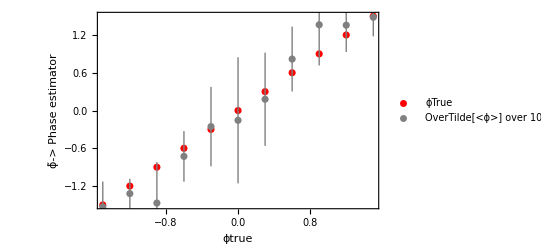

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevRMSE}],PlotStyle->{Gray}, PlotLegends->{"OverTilde[<ϕ>] over 100 trials ± RMSE"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

```mathematica
(*Median +- MAD*)
```

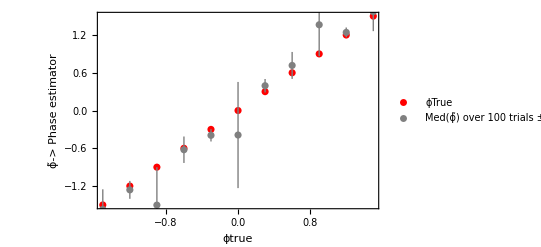

```mathematica
Show[ListPlot[Thread[{PlotResults,PlotResults}],PlotStyle->{Red,Thick},PlotLegends->{"ϕTrue"}],ListPlot[Thread[{PlotResults,PlotDevMAD}],PlotStyle->{Gray}, PlotLegends->{"Med(ϕ̃) over 100 trials ± MAD"}], Frame->True,FrameTicks->Automatic,FrameLabel->{"ϕtrue",Style["ϕ̃-> Phase estimator",Thick]}]
```

## E. Probability of being unlucky - Check using MC

### Nph = 3

#### Vary ϕ_true for Δ_initial= π/10, π/5, 3π/10, 2π/5, π/2, π and plot probability of convergence over 100 trials

```mathematica
Data=Table[
GridOfϕTrue=Table[
ntrial=100;
listOfPhaseEstimators=Table[
(*Set the number of photons*)
nph=3;
(*Start with some (*interval [-Delta,Delta]*)*)
initInterval =del*π/10;
(*Nature chooses the true value for the phase in the interval (unknown to the experimentalist)*)
ϕTrue =phitrue;
(*The experimentalist starts with center point Subscript[ϕ, 0]=0 and uncertainty Subscript[Δ, 0]=initInterval.*)
ϕtilde=0;
Δinit = initInterval;
nshots=30;
(*can variance and probability be calculated only once?*)
Clear[delta];
partialvariance=GetVariance[1,nph,delta];
(*The output is : {Subscript[P, 1] Subscript[(δϕ^2), 1],Subscript[P, 2] Subscript[(δϕ^2), 2],...}. Need to divide probability from variance*)
δϕsquared = Table[partialvariance[[n]]/Pm[[n]],{n,1,nph+1}];
phitilde=Table[
delta=Δinit;
(*list of P(m|ϕ) are the probabilities of getting outcome m*)
(*The experimentalist constructs an optimal one-shot input state for this uncertainty interval,*)
(*Plug N00N in N00N regime, Gaussian in Gaussian regime*)
If[Δinit*nph> 5,OptState=PlugGSBS[](*Print["Gaussian"];*),OptState=PlugN00NSBS[](*Print["N00N"];*)];
(*changed here*)
UnshiftedOptState=OptState;
Table[OptState[[1,n,2]] += n ϕtilde,{n,1,nph+1}];
(*The experimentalist makes measurements m with the following probabilities*)
(*P(m|ϕ)*)
prob=Re[listOfPmϕ/.OptState];
(*This is the probability distribution that nature has/knows*)
prob2=Re[listOfPmϕ/.UnshiftedOptState/.ϕ->(ϕTrue)];
probDistrib = Accumulate[prob2[[1]]];
(*mRand is a uniformly distributed random real between 0 and 1*)
SeedRandom[];
mRand=Random[];
(*if mRand<probDistrib[[m]], outcome m occured experimentally*)
outcomeOccured =Max[Table[If[mRand>probDistrib[[m]],m,0],{m,1,nph+1}]]+1;
(*changed here*)
Indvariance=δϕsquared/.OptState;
variance=Indvariance[[1,outcomeOccured]];
Probability1stshot=prob2[[1,outcomeOccured]];
(*normalize variance*)
normalizedvariance=variance;
Δnext = √(12*variance);
(*varianceDistrib[[1,outcomeOccured]]*)
(*changed here*)
phaseEstimators=listOfϕ1/.OptState;
(*and the following phase estimator*)
ϕtilde+=phaseEstimators[[1,outcomeOccured]];
(*Input state of the second shot gets phase shifted by this phase above*)
Δinit=Δnext;
(*{normalizedvariance/(initInterval^2/12),ϕtilde,initInterval,OptState,outcomeOccured,Δnext,prob2}*)
,{shot,1, nshots}];
{Δnext,ϕtilde},{trial,1,ntrial}];
(*finds the mean of the varRatio over ntrials for a particular Δini*)
{ϕTrue,ϕTrue/(initInterval/2),listOfPhaseEstimators},{phitrue,-del*π/20,del*π/20,del*π/100}];
IfConverge=MatrixForm[Table[ProbOfTrue=0;{GridOfϕTrue[[n,1]],GridOfϕTrue[[n,2]],Table[If[GridOfϕTrue[[n,3,trial,2]]>(GridOfϕTrue[[n,1]]-GridOfϕTrue[[n,3,trial,1]]/2)&&GridOfϕTrue[[n,3,trial,2]]<(GridOfϕTrue[[n,1]]+GridOfϕTrue[[n,3,trial,1]]/2),ProbOfTrue+=1;GridOfϕTrue[[n,3,trial,2]],GridOfϕTrue[[n,3,trial,2]](*{GridOfϕTrue[[n,3,trial,2]],True}{GridOfϕTrue[[n,3,trial,2]],False}*)],{trial,1,ntrial}],N[ProbOfTrue/ntrial],del π/10},{n,1,Length[GridOfϕTrue]}]];
IfConverge1 = MatrixForm[Drop[IfConverge[[1]],None,{3}]],{del,{1,2,3,4,5,10}}];
```

```mathematica
(*Subscript[ϕ, true],Subscript[ϕ, true]/(Δ/2), probability of converging, Subscript[Δ, initial] *)
```

```mathematica
Data
```

{(-π/20 | -1 | 0.18 | π/10
-π/25 | -4/5 | 0.27 | π/10
-(3 π)/100 | -3/5 | 0.26 | π/10
-π/50 | -2/5 | 0.32 | π/10
-π/100 | -1/5 | 0.33 | π/10
0 | 0 | 0.4 | π/10
π/100 | 1/5 | 0.41 | π/10
π/50 | 2/5 | 0.29 | π/10
(3 π)/100 | 3/5 | 0.35 | π/10
π/25 | 4/5 | 0.25 | π/10
π/20 | 1 | 0.2 | π/10),(-π/10 | -1 | 0.58 | π/5
-(2 π)/25 | -4/5 | 0.35 | π/5
-(3 π)/50 | -3/5 | 0.3 | π/5
-π/25 | -2/5 | 0.2 | π/5
-π/50 | -1/5 | 0.15 | π/5
0 | 0 | 0.14 | π/5
π/50 | 1/5 | 0.13 | π/5
π/25 | 2/5 | 0.3 | π/5
(3 π)/50 | 3/5 | 0.24 | π/5
(2 π)/25 | 4/5 | 0.43 | π/5
π/10 | 1 | 0.57 | π/5),(-(3 π)/20 | -1 | 0.82 | (3 π)/10
-(3 π)/25 | -4/5 | 0.59 | (3 π)/10
-(9 π)/100 | -3/5 | 0.37 | (3 π)/10
-(3 π)/50 | -2/5 | 0.29 | (3 π)/10
-(3 π)/100 | -1/5 | 0.24 | (3 π)/10
0 | 0 | 0.27 | (3 π)/10
(3 π)/100 | 1/5 | 0.24 | (3 π)/10
(3 π)/50 | 2/5 | 0.28 | (3 π)/10
(9 π)/100 | 3/5 | 0.29 | (3 π)/10
(3 π)/25 | 4/5 | 0.6 | (3 π)/10
(3 π)/20 | 1 | 0.74 | (3 π)/10),(-π/5 | -1 | 0.6 | (2 π)/5
-(4 π)/25 | -4/5 | 0.88 | (2 π)/5
-(3 π)/25 | -3/5 | 0.5 | (2 π)/5
-(2 π)/25 | -2/5 | 0.31 | (2 π)/5
-π/25 | -1/5 | 0.25 | (2 π)/5
0 | 0 | 0.26 | (2 π)/5
π/25 | 1/5 | 0.24 | (2 π)/5
(2 π)/25 | 2/5 | 0.3 | (2 π)/5
(3 π)/25 | 3/5 | 0.43 | (2 π)/5
(4 π)/25 | 4/5 | 0.86 | (2 π)/5
π/5 | 1 | 0.58 | (2 π)/5),(-π/4 | -1 | 0.35 | π/2
-π/5 | -4/5 | 0.66 | π/2
-(3 π)/20 | -3/5 | 0.57 | π/2
-π/10 | -2/5 | 0.45 | π/2
-π/20 | -1/5 | 0.23 | π/2
0 | 0 | 0.26 | π/2
π/20 | 1/5 | 0.18 | π/2
π/10 | 2/5 | 0.29 | π/2
(3 π)/20 | 3/5 | 0.57 | π/2
π/5 | 4/5 | 0.68 | π/2
π/4 | 1 | 0.32 | π/2),(-π/2 | -1 | 0.95 | π
-(2 π)/5 | -4/5 | 0.54 | π
-(3 π)/10 | -3/5 | 0.14 | π
-π/5 | -2/5 | 0.77 | π
-π/10 | -1/5 | 0.35 | π
0 | 0 | 0.3 | π
π/10 | 1/5 | 0.39 | π
π/5 | 2/5 | 0.78 | π
(3 π)/10 | 3/5 | 0.26 | π
(2 π)/5 | 4/5 | 0.4 | π
π/2 | 1 | 0.88 | π)}

```mathematica
(*y -> probability of converging after 20 shots*)
```

```mathematica
y=MatrixForm[Table[Table[Data[[del,1,n,3]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.18 | 0.27 | 0.26 | 0.32 | 0.33 | 0.4 | 0.41 | 0.29 | 0.35 | 0.25 | 0.2
0.58 | 0.35 | 0.3 | 0.2 | 0.15 | 0.14 | 0.13 | 0.3 | 0.24 | 0.43 | 0.57
0.82 | 0.59 | 0.37 | 0.29 | 0.24 | 0.27 | 0.24 | 0.28 | 0.29 | 0.6 | 0.74
0.6 | 0.88 | 0.5 | 0.31 | 0.25 | 0.26 | 0.24 | 0.3 | 0.43 | 0.86 | 0.58
0.35 | 0.66 | 0.57 | 0.45 | 0.23 | 0.26 | 0.18 | 0.29 | 0.57 | 0.68 | 0.32
0.95 | 0.54 | 0.14 | 0.77 | 0.35 | 0.3 | 0.39 | 0.78 | 0.26 | 0.4 | 0.88)

```mathematica
(*Standard error for sample proportion of success p is √(p(1-p)/100)*)
```

```mathematica
z1=MatrixForm[Table[Table[√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial),{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.0384187 | 0.0443959 | 0.0438634 | 0.0466476 | 0.0470213 | 0.0489898 | 0.0491833 | 0.0453762 | 0.047697 | 0.0433013 | 0.04
0.0493559 | 0.047697 | 0.0458258 | 0.04 | 0.0357071 | 0.0346987 | 0.0336303 | 0.0458258 | 0.0427083 | 0.0495076 | 0.0495076
0.0384187 | 0.0491833 | 0.0482804 | 0.0453762 | 0.0427083 | 0.0443959 | 0.0427083 | 0.0448999 | 0.0453762 | 0.0489898 | 0.0438634
0.0489898 | 0.0324962 | 0.05 | 0.0462493 | 0.0433013 | 0.0438634 | 0.0427083 | 0.0458258 | 0.0495076 | 0.0346987 | 0.0493559
0.047697 | 0.0473709 | 0.0495076 | 0.0497494 | 0.0420833 | 0.0438634 | 0.0384187 | 0.0453762 | 0.0495076 | 0.0466476 | 0.0466476
0.0217945 | 0.0498397 | 0.0346987 | 0.0420833 | 0.047697 | 0.0458258 | 0.048775 | 0.0414246 | 0.0438634 | 0.0489898 | 0.0324962)

```mathematica
z=MatrixForm[Table[Table[Around[Data[[del,1,n,3]],√(((Data[[del,1,n,3]])(1-Data[[del,1,n,3]]))/ntrial)],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(0.180.04 | 0.270.04 | 0.260.04 | 0.320.05 | 0.330.05 | 0.400.05 | 0.410.05 | 0.290.05 | 0.350.05 | 0.250.04 | 0.200.04
0.580.05 | 0.350.05 | 0.300.05 | 0.200.04 | 0.150.04 | 0.1400.035 | 0.1300.034 | 0.300.05 | 0.240.04 | 0.430.05 | 0.570.05
0.820.04 | 0.590.05 | 0.370.05 | 0.290.05 | 0.240.04 | 0.270.04 | 0.240.04 | 0.280.04 | 0.290.05 | 0.600.05 | 0.740.04
0.600.05 | 0.8800.032 | 0.500.05 | 0.310.05 | 0.250.04 | 0.260.04 | 0.240.04 | 0.300.05 | 0.430.05 | 0.8600.035 | 0.580.05
0.350.05 | 0.660.05 | 0.570.05 | 0.450.05 | 0.230.04 | 0.260.04 | 0.180.04 | 0.290.05 | 0.570.05 | 0.680.05 | 0.320.05
0.9500.022 | 0.540.05 | 0.1400.035 | 0.770.04 | 0.350.05 | 0.300.05 | 0.390.05 | 0.780.04 | 0.260.04 | 0.400.05 | 0.8800.032)

```mathematica
(*x -> ϕTrue/(Δ/2)*)
```

```mathematica
x=MatrixForm[Table[Table[Data[[del,1,n,2]],{n,1, Length[Data[[1,1]]]}],{del,1, Length[Data]}]]
```

(-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1
-1 | -4/5 | -3/5 | -2/5 | -1/5 | 0 | 1/5 | 2/5 | 3/5 | 4/5 | 1)

```mathematica
plot = MatrixForm[Table[Thread[{x[[1,n]],y[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.18) | (-4/5
0.27) | (-3/5
0.26) | (-2/5
0.32) | (-1/5
0.33) | (0
0.4) | (1/5
0.41) | (2/5
0.29) | (3/5
0.35) | (4/5
0.25) | (1
0.2)
(-1
0.58) | (-4/5
0.35) | (-3/5
0.3) | (-2/5
0.2) | (-1/5
0.15) | (0
0.14) | (1/5
0.13) | (2/5
0.3) | (3/5
0.24) | (4/5
0.43) | (1
0.57)
(-1
0.82) | (-4/5
0.59) | (-3/5
0.37) | (-2/5
0.29) | (-1/5
0.24) | (0
0.27) | (1/5
0.24) | (2/5
0.28) | (3/5
0.29) | (4/5
0.6) | (1
0.74)
(-1
0.6) | (-4/5
0.88) | (-3/5
0.5) | (-2/5
0.31) | (-1/5
0.25) | (0
0.26) | (1/5
0.24) | (2/5
0.3) | (3/5
0.43) | (4/5
0.86) | (1
0.58)
(-1
0.35) | (-4/5
0.66) | (-3/5
0.57) | (-2/5
0.45) | (-1/5
0.23) | (0
0.26) | (1/5
0.18) | (2/5
0.29) | (3/5
0.57) | (4/5
0.68) | (1
0.32)
(-1
0.95) | (-4/5
0.54) | (-3/5
0.14) | (-2/5
0.77) | (-1/5
0.35) | (0
0.3) | (1/5
0.39) | (2/5
0.78) | (3/5
0.26) | (4/5
0.4) | (1
0.88))

```mathematica
plotStdError= MatrixForm[Table[Thread[{x[[1,n]],z[[1,n]]}],{n,1,Length[Data]}]]
```

((-1
0.180.04) | (-4/5
0.270.04) | (-3/5
0.260.04) | (-2/5
0.320.05) | (-1/5
0.330.05) | (0
0.400.05) | (1/5
0.410.05) | (2/5
0.290.05) | (3/5
0.350.05) | (4/5
0.250.04) | (1
0.200.04)
(-1
0.580.05) | (-4/5
0.350.05) | (-3/5
0.300.05) | (-2/5
0.200.04) | (-1/5
0.150.04) | (0
0.1400.035) | (1/5
0.1300.034) | (2/5
0.300.05) | (3/5
0.240.04) | (4/5
0.430.05) | (1
0.570.05)
(-1
0.820.04) | (-4/5
0.590.05) | (-3/5
0.370.05) | (-2/5
0.290.05) | (-1/5
0.240.04) | (0
0.270.04) | (1/5
0.240.04) | (2/5
0.280.04) | (3/5
0.290.05) | (4/5
0.600.05) | (1
0.740.04)
(-1
0.600.05) | (-4/5
0.8800.032) | (-3/5
0.500.05) | (-2/5
0.310.05) | (-1/5
0.250.04) | (0
0.260.04) | (1/5
0.240.04) | (2/5
0.300.05) | (3/5
0.430.05) | (4/5
0.8600.035) | (1
0.580.05)
(-1
0.350.05) | (-4/5
0.660.05) | (-3/5
0.570.05) | (-2/5
0.450.05) | (-1/5
0.230.04) | (0
0.260.04) | (1/5
0.180.04) | (2/5
0.290.05) | (3/5
0.570.05) | (4/5
0.680.05) | (1
0.320.05)
(-1
0.9500.022) | (-4/5
0.540.05) | (-3/5
0.1400.035) | (-2/5
0.770.04) | (-1/5
0.350.05) | (0
0.300.05) | (1/5
0.390.05) | (2/5
0.780.04) | (3/5
0.260.04) | (4/5
0.400.05) | (1
0.8800.032))

```mathematica
(*For different values of quantity A = ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photons*)
```

```mathematica
(*color plot distinguishing different Δinitials*)
```

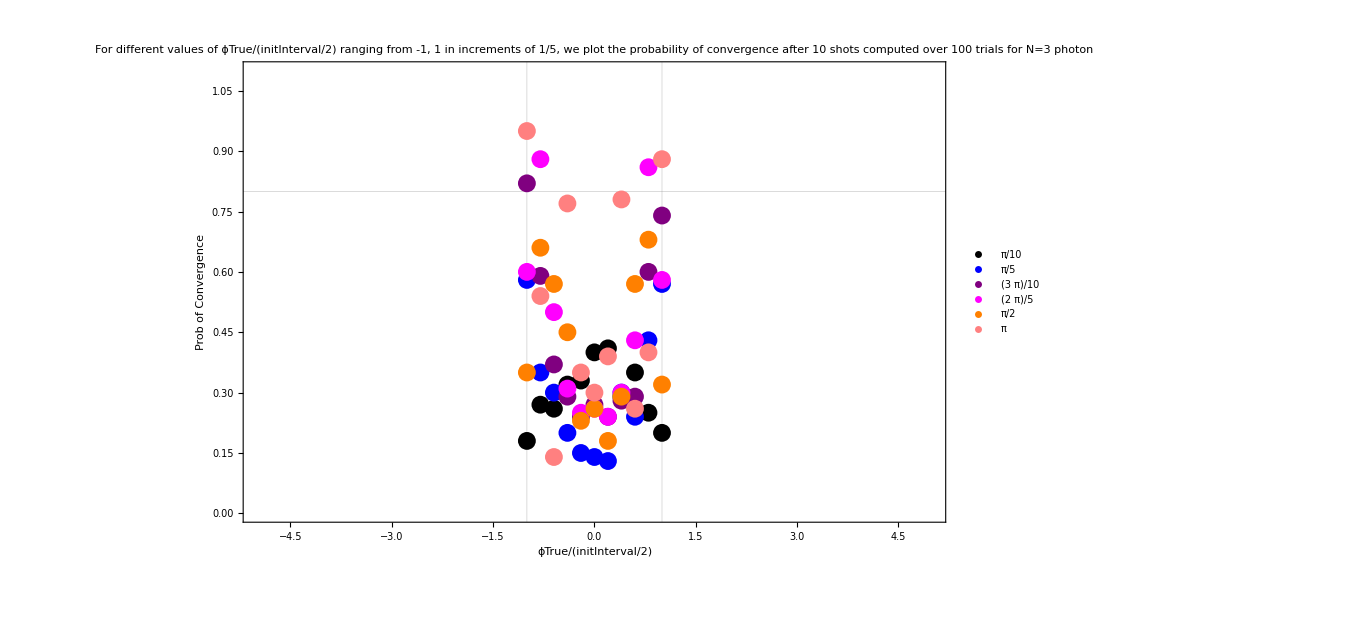

```mathematica
plot31=Show[ListPlot[plot[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence after 10 shots computed over 100 trials for N=3 photon",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*color plot with error bars*)
```

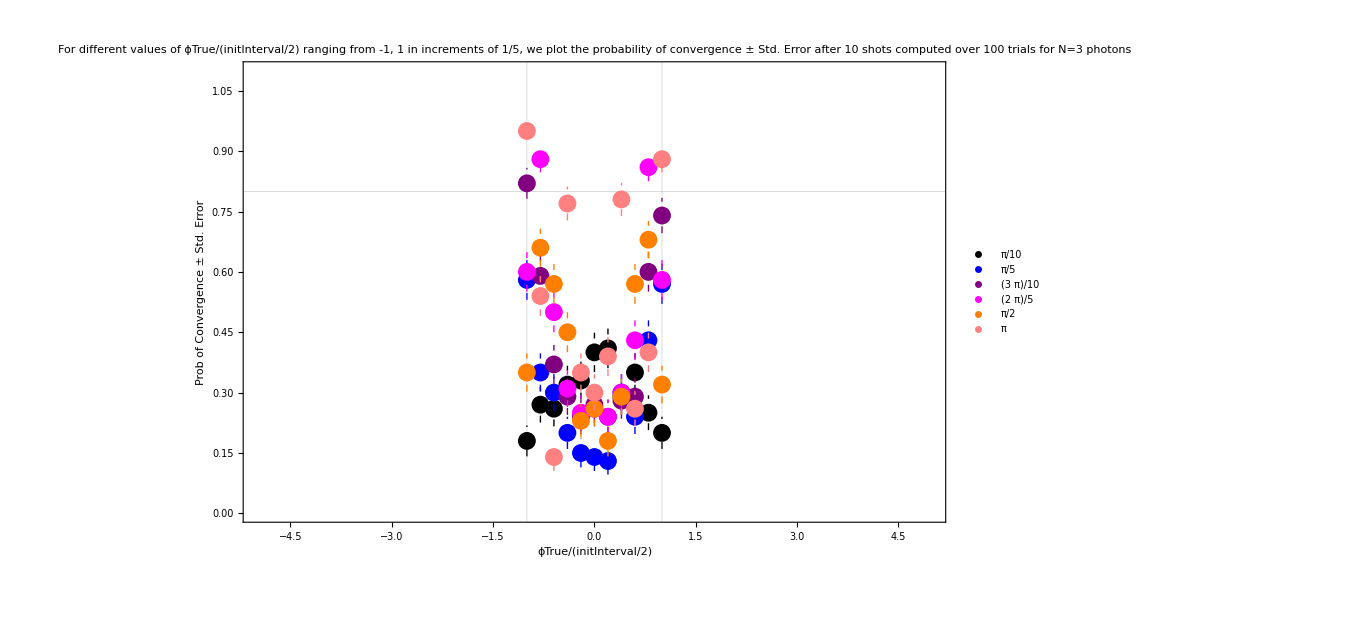

```mathematica
plot32=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Black, Dashed},PlotLabel->"For different values of ϕTrue/(initInterval/2) ranging from -1, 1 in increments of 1/5, we plot the probability of convergence ± Std. Error after 10 shots computed over 100 trials for N=3 photons",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Blue,Dashed},PlotLegends->{(2π)/10}],ListPlot[plotStdError[[1,3]],PlotStyle->{Purple, Dashed},PlotLegends->{(3π)/10}],ListPlot[plotStdError[[1,4]],PlotStyle->{Magenta,Dashed},PlotLegends->{(4π)/10}],ListPlot[plotStdError[[1,5]],PlotStyle->{Orange,Dashed},PlotLegends->{(5π)/10}],ListPlot[plotStdError[[1,6]],PlotStyle->{Pink,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{1000, Automatic}]
```

```mathematica
(*Monochromatic plot distinguishing different N*)
```

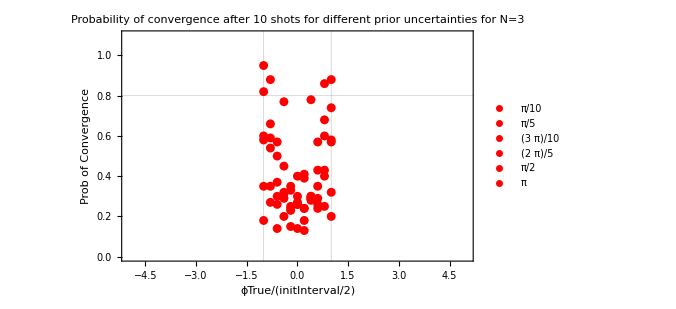

```mathematica
plot33=Show[ListPlot[plot[[1,1]],PlotStyle->{Red, Dashed},PlotLabel->"Probability of convergence after 10 shots for different prior uncertainties for N=3",PlotLegends->{π/10},GridLines->{{-1,1},{0.8}}],ListPlot[plot[[1,2]],PlotStyle->{Red,Dashed},PlotLegends->{(2π)/10}],ListPlot[plot[[1,3]],PlotStyle->{Red, Dashed},PlotLegends->{(3π)/10}],ListPlot[plot[[1,4]],PlotStyle->{Red,Dashed},PlotLegends->{(4π)/10}],ListPlot[plot[[1,5]],PlotStyle->{Red,Dashed},PlotLegends->{(5π)/10}],ListPlot[plot[[1,6]],PlotStyle->{Red,Dashed},PlotLegends->{π}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0},ImageSize->{500, Automatic}]
```

```mathematica
(*Monochromatic plot with error bars*)
```

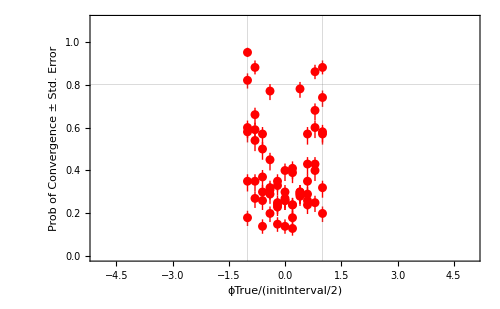

```mathematica
plot34=Show[ListPlot[plotStdError[[1,1]],PlotStyle->{Red, Dashed},GridLines->{{-1,1},{0.8}}],ListPlot[plotStdError[[1,2]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,3]],PlotStyle->{Red, Dashed}],ListPlot[plotStdError[[1,4]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,5]],PlotStyle->{Red,Dashed}],ListPlot[plotStdError[[1,6]],PlotStyle->{Red,Dashed}],PlotRange->{{-5,5},{0,1.1}}, Frame->True,FrameLabel->{"ϕTrue/(initInterval/2)",Style["Prob of Convergence ± Std. Error",Thick]}, FrameTicks->Automatic, AxesOrigin-> {0,0}]
```

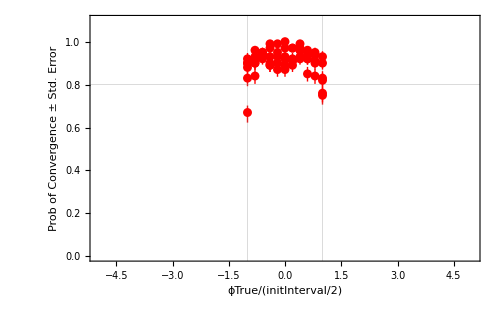
```mathematica
plot34=-Graphics-;
```

```mathematica
(*Average of all the points in the interval between -1,1*)
(*Average y*)
```

```mathematica
Average3y = Table[Mean[y[[1,n]]],{n,1,6}]
```

{0.296364,0.308182,0.43,0.473636,0.414545,0.523636}

```mathematica
(*Average σ -> Subscript[σ, avg]=*)
```

```mathematica
Average3σ=Table[ 1/11 √Sum[z1[[1,m,n]]^2,{n,1,11}],{m,1,6}]
```

{0.0136018,0.0131259,0.0135765,0.0134561,0.0139296,0.0127869}

```mathematica
(*(Subscript[y, i] Subscript[σ, i])*)
```

```mathematica
Average3=MatrixForm[Thread[{Average3y,Average3σ}]]
```

(0.296364 | 0.0136018
0.308182 | 0.0131259
0.43 | 0.0135765
0.473636 | 0.0134561
0.414545 | 0.0139296
0.523636 | 0.0127869)

```mathematica
Average3=Table[Around[Average3[[1,n,1]],Average3[[1,n,2]]],{n,1,Length[Data]}]
```

{0.2960.014,0.3080.013,0.4300.014,0.4740.013,0.4150.014,0.5240.013}

```mathematica
(*Total Average*)
```

```mathematica
TotalAverage3y=Mean[Average3[[All,1]]]
```

0.407727

```mathematica
TotalAverage3σ = 1/6 √Sum[Average3[[n,2]]^2,{n,1,6}]
```

0.00547779

```mathematica
TotalAverage3= Around[TotalAverage3y,TotalAverage3σ]
```

0.4080.005

```mathematica
TotalAverage3
```

0.4080.005